```mathematica
AppendTo[$Path,"~/projects/KnotTheory/trunk/"];
```

```mathematica
<<KnotTheory`
```

Loading KnotTheory` version of January 20, 2015, 10:42:19.1122.
Read more at http://katlas.org/wiki/KnotTheory.

```mathematica
<<QuantumGroups`
```

Loading QuantumGroups` version 2.0
Read more at http://katlas.math.toronto.edu/wiki/QuantumGroups

Remember to set QuantumGroupsDataDirectory[] to the appropriate path, if you've downloaded precomputed data.

```mathematica
brace[l_]:=brace[0,l]
brace[k_,l_]:=w^k v^l+w^-k v^-l
bracket[k_,l_]:=w^k v^l-w^-k v^-l
```

```mathematica
dw=-(brace[2]bracket[1,5]bracket[1,-6])/(bracket[1,0]bracket[1,-1]);
```

```mathematica
Clear[i]
```

```mathematica
i[X_Times]:=i/@X
i[Power[X_,k_]]:=i[X]^k
i[n_Integer]:=n
```

```mathematica
i[1-x_]:=-i[x-1]
i[v]=v;
i[w]=w;
i[q]=q;
i[X_Plus]/;X⟦1⟧=!=1∧X⟦1⟧=!=-1:=X⟦1⟧i[Expand[X/X⟦1⟧]]
```

```mathematica
c[n_,z_]:=
With[{a=Exponent[z,v],b=Exponent[z,w]},
Product[(PowerExpand[(v^a w^b)^(n/(2d))]brk[(n b)/(2 d),(n a)/(2d)])^MoebiusMu[d],{d,Divisors[n]}]
]
```

```mathematica
cq[n_]:=
Product[(q^(n/(2d))qi[n/(2d)])^MoebiusMu[d],{d,Divisors[n]}]
```

```mathematica
Do[i[Cyclotomic[n,z]]=c[n,z],{n,1,20},{z,DeleteCases[Flatten[Table[v^k w^l,{k,-12,12},{l,-6,6}]],1]}];
```

```mathematica
Do[i[Cyclotomic[n,z]]=c[n,z],{n,1,20},{z,DeleteCases[Table[v^k,{k,-50,50}],1]}];
```

```mathematica
Do[i[Cyclotomic[n,q]]=cq[n],{n,1,100}]
```

KnotTheory::loading: Loading precomputed data in "PD4Knots`".

KnotTheory::credits: "DrawPD was written by Emily Redelmeier at the University of Toronto in the summers of 2003 and 2004."

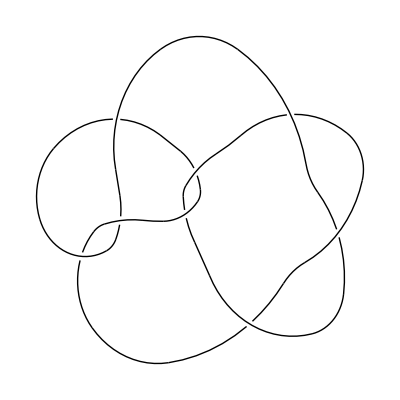

```mathematica
DrawPD[Knot[8,19]]
```

```mathematica
Writhe[k:(_Knot|_Link|_BR)]:=Writhe[PD[k]]
Writhe[p_PD]:=With[{o=OPD[p]},Count[o,_Xp]-Count[o,_Xn]]
```

```mathematica
RotateBox[X_,0]:=X
RotateBox[RotateBox[X_,k_],l_]:=RotateBox[X,k+l]
```

```mathematica
ClearAll[PlanarDiagram]
```

```mathematica
SetAttributes[PlanarDiagram,{Flat,Orderless,OneIdentity}]
```

```mathematica
PlanarDiagram[Box[{a_,a_,b___},X_]]:=PlanarDiagram[Box[{b},Stitch[X]]]
PlanarDiagram[Box[{a__,b_,b_,c___},X_]]:=PlanarDiagram[Box[{b,b,c,a},RotateBox[X,Length[{a}]]]]
```

```mathematica
PlanarDiagram[Box[{b_,c_,d_},X_],Box[{d_,c_,e___},Y_]]:=PlanarDiagram[Box[{b,e},Multiply[2][X,Y]]]
PlanarDiagram[Box[{a_,b_,c_,d_},X_],Box[{d_,c_,e___},Y_]]:=PlanarDiagram[Box[{a,b,e},Multiply[2][X,Y]]]
PlanarDiagram[Box[{a___,b_,c_,d___},X_],Box[{e___,c_,b_,f___},Y_]]:=PlanarDiagram[Box[{d,a,b,c},RotateBox[X,-Length[{d}]]],Box[{c,b,f,e},RotateBox[Y,Length[{e}]]]]
PlanarDiagram[Box[{a_,b___,c_},X_],Box[{d___,a_,c_,e___},Y_]]:=PlanarDiagram[Box[{b,c,a},RotateBox[X,1]],Box[{a,c,e,d},RotateBox[Y,Length[{d}]]]]
PlanarDiagram[Box[{a___,b_,c_,d__},X_],Box[{b_,e___,c_},Y_]]:=PlanarDiagram[Box[{d,a,b,c},RotateBox[X,-Length[{d}]]],Box[{c,b,e},RotateBox[Y,-1]]]
PlanarDiagram[Box[{a_,b___,c_},X_],Box[{c_,d___,a_},Y_]]:=PlanarDiagram[Box[{b,c,a},RotateBox[X,1]],Box[{a,c,d},RotateBox[Y,-1]]]
```

```mathematica
PlanarDiagram[Box[{a___,b_,c___},X_],Box[{d___,b_,e___},Y_]]:=PlanarDiagram[Box[{c,a,e,d},Multiply[1][RotateBox[X,-Length[{c}]],RotateBox[Y,Length[{d}]]]]]
```

```mathematica
PlanarDiagram[p_PD]:=PlanarDiagram@@(p/.{X[a_,b_,c_,d_]:>Box[{c,d,a,b},X],Y[a_,b_,c_]:>Box[{a,b,c},Y]})
```

```mathematica
PlanarDiagram[K:(_Knot|_Link)]:=Module[{result},
result=Quiet[PlanarDiagram[PD[K]],$IterationLimit::itlim];
If[FreeQ[result,Hold],
PlanarDiagram[K]=result,
$Failed]
]
```

```mathematica
PlanarDiagram[Knot[8,19]]
```

PlanarDiagram[Box[{},Stitch[Stitch[RotateBox[Multiply[2][X,Multiply[2][RotateBox[Multiply[2][RotateBox[X,-1],RotateBox[X,-1]],-1],RotateBox[Multiply[2][RotateBox[Multiply[2][RotateBox[X,-1],RotateBox[X,-1]],-1],RotateBox[Multiply[2][RotateBox[Multiply[2][RotateBox[X,-1],RotateBox[X,-1]],-2],RotateBox[X,1]],-1]],1]]],1]]]]]

```mathematica
Cases[AllKnots[{3,11}],K_/;PlanarDiagram[K]⟦1,1⟧≠{}]
```

KnotTheory::loading: Loading precomputed data in "DTCode4KnotsTo11`".

KnotTheory::credits: "The GaussCode to PD conversion was written by Siddarth Sankaran at the University of Toronto in the summer of 2005."

{}

```mathematica
(*Cases[AllKnots[12],K_/;PlanarDiagram[K]===$Failed∨PlanarDiagram[K]⟦1,1⟧=!={}]==={Knot[12,Alternating,1251]}*)
```

```mathematica
(*Cases[AllKnots[13],K_/;PlanarDiagram[K]===$Failed∨PlanarDiagram[K]⟦1,1⟧=!={}]*)
```

```mathematica
(*Cases[AllKnots[14],K_/;PlanarDiagram[K]===$Failed∨PlanarDiagram[K]⟦1,1⟧=!={}]*)
```

```mathematica
(*Cases[AllKnots[15],K_/;PlanarDiagram[K]===$Failed∨PlanarDiagram[K]⟦1,1⟧=!={}]*)
```

```mathematica
(*Cases[AllKnots[16],K_/;PlanarDiagram[K]===$Failed∨PlanarDiagram[K]⟦1,1⟧=!={}]*)
```

KnotTheory::loading: Loading precomputed data in "KnotTheory/12A.dts".

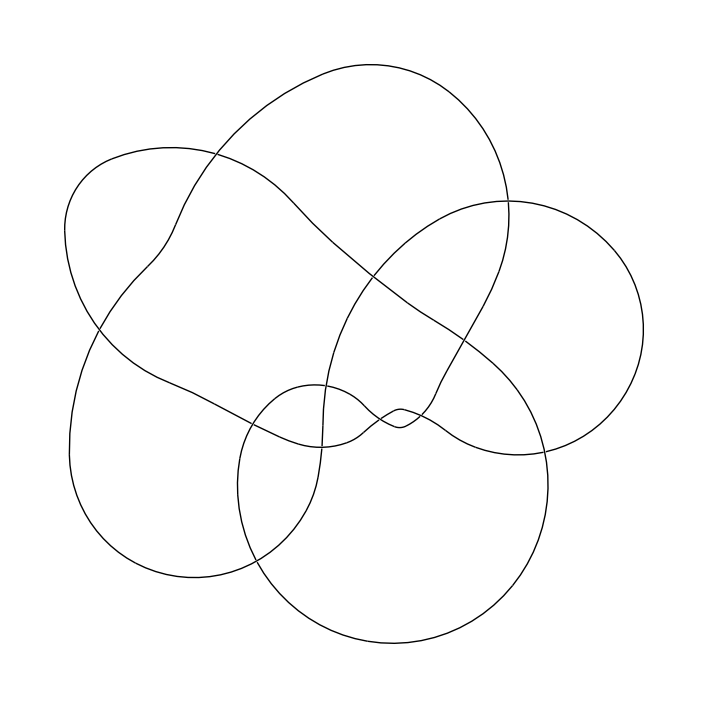

```mathematica
DrawPD[Knot[12,Alternating,1251]]
```

### Loading matrices

```mathematica
Clear[QESRotation,QESBraiding,QESInverseBraiding,QESCupCap,QESCap,QESCup,QESI,QESH,QESFork,QESFuse]
```

```mathematica
ZeroMatrix[n_]:=Table[0,{n},{n}]
ZeroMatrix[n_,m_]:=Table[0,{n},{m}]
```

```mathematica
QESDimension[n_]:=Length[QESRotation[n]]
```

```mathematica
QESId[n_]:=IdentityMatrix[QESDimension[n]]
QESZero[n_,m_]:=ZeroMatrix[QESDimension[n],QESDimension[m]]
QESRotation[0]:={{1}}
QESRotation[1]:={}
QESRotation[n_]:=QESRotation[n]=Get[FileNameJoin[{NotebookDirectory[],ToString[n]<>"-box-rotation-matrix.m"}]];
QESRotation[n_,k_]/;k<0∨k≥n:=QESRotation[n,Mod[k,n]]
QESRotation[n_,0]:=IdentityMatrix[Length[QESRotation[n]]]
QESRotation[n_,1]:=QESRotation[n]
QESRotation[n_,k_]:=QESRotation[n,k]=Together[QESRotation[n].QESRotation[n,k-1]]
QESBraiding[n_]:=QESBraiding[n]=Get[FileNameJoin[{NotebookDirectory[],ToString[n]<>"-box-braiding-matrix.m"}]];
QESBraiding[n_,k_]:=QESBraiding[n,k]=Together[QESRotation[n,-k].QESBraiding[n].QESRotation[n,k]]
QESInverseBraiding[n_]:=QESInverseBraiding[n]=Get[FileNameJoin[{NotebookDirectory[],ToString[n]<>"-box-inverse-braiding-matrix.m"}]];
QESInverseBraiding[n_,k_]:=QESInverseBraiding[n,k]=Together[QESRotation[n,-k].QESInverseBraiding[n].QESRotation[n,k]]
QESCupCap[n_]:=QESCupCap[n]=Together[QESCup[n-2].QESCap[n]]
QESCupCap[3]={{0}};
QESCup[0]={{1}};
QESCup[1]={{}};
QESCup[n_]:=QESCup[n]=Get[FileNameJoin[{NotebookDirectory[],ToString[n]<>"-box-cup-matrix.m"}]]
QESCap[2]={{d}};
QESCap[n_]:=QESCap[n]=Get[FileNameJoin[{NotebookDirectory[],ToString[n]<>"-box-cap-matrix.m"}]]
QESI[n_]:=QESI[n]=Together[QESFork[n-1].QESFuse[n]]
QESFork[n_]:=QESFork[n]=Get[FileNameJoin[{NotebookDirectory[],ToString[n]<>"-box-fork-matrix.m"}]]
QESFuse[n_]:=QESFuse[n]=Get[FileNameJoin[{NotebookDirectory[],ToString[n]<>"-box-fuse-matrix.m"}]]
QESH[n_]:=QESH[n]=Get[FileNameJoin[{NotebookDirectory[],ToString[n]<>"-box-H-matrix.m"}]]
```

### Verifying matrices

```mathematica
Table[Together[QESRotation[k,k-1].QESRotation[k]]==QESId[k],{k,2,6}]
```

{True,True,True,True,True}

```mathematica
Table[QESCupCap[k].QESCupCap[k]==d QESCupCap[k],{k,2,6}]
```

{True,True,True,True,True}

```mathematica
Table[QESFuse[k+2].QESCup[k]==QESZero[k+1,k],{k,1,4}]
```

{True,True,True,True}

```mathematica
Table[Together[QESBraiding[k].QESInverseBraiding[k]]==QESId[k],{k,2,6}]
```

{True,True,True,True,True}

```mathematica
Table[Together[QESInverseBraiding[k].QESBraiding[k]]==QESId[k],{k,2,6}]
```

{True,True,True,True,True}

```mathematica
Table[QESBraiding[k+1].QESFork[k]==(-v^6)QESFork[k],{k,2,5}]
```

{True,True,True,True}

```mathematica
Table[QESInverseBraiding[k+1].QESFork[k]==(-v^-6)QESFork[k],{k,2,5}]
```

{True,True,True,True}

```mathematica
Table[QESBraiding[k+2].QESCup[k]==(v^12)QESCup[k],{k,2,4}]
```

{True,True,True}

```mathematica
Table[QESInverseBraiding[k+2].QESCup[k]==(v^-12)QESCup[k],{k,2,4}]
```

{True,True,True}

```mathematica
(*Table[Together[QESBraiding[k,0].QESBraiding[k,1].QESBraiding[k,0]-QESBraiding[k,1].QESBraiding[k,0].QESBraiding[k,1]]==QESZero[k],{k,2,6}]*)
```

```mathematica
(* There's still lots more interesting stuff that could be verified here. *)
```

```mathematica
i[PolynomialLCM@@Denominator[Flatten[Table[Together[QESCupCap[k]/.d->dw],{k,2,6}]]]]
```

-(v^33 w^4 brk[0,1] brk[0,3] brk[0,6] brk[1,-1] brk[1,0] i[1+w^2/v^6+v^4 w^2+w^4/v^2]^2)/brk[0,2]

```mathematica
PolynomialLCM@@Denominator[Flatten[Table[QESI[k],{k,3,6}]]]
```

v^18 (1+v^2) (1-v+v^2) (1+v+v^2) (1+v^4)^2 (1+d v^2+v^4) (1+d v^8+v^16)^3

```mathematica
i[PolynomialLCM@@Denominator[Flatten[Table[Together[QESI[k]/.d->dw],{k,3,6}]]]]
```

(v^40 w^2 brk[0,3]^2 brk[0,6] i[1+w^2/v^6+v^4 w^2+w^4/v^2]^3)/brk[0,2]

```mathematica
PolynomialLCM@@Denominator[Flatten[Table[QESH[k],{k,3,6}]]]
```

v^16 (1+v^2) (1-v+v^2)^2 (1+v+v^2)^2 (1+v^4)^2 (1+d v^2+v^4) (1+d v^8+v^16)^4

```mathematica
i[PolynomialLCM@@Denominator[Flatten[Table[Together[QESH[k]/.d->dw],{k,3,6}]]]]
```

(v^48 w^2 brk[0,1] brk[0,3]^3 brk[0,6] i[1+w^2/v^6+v^4 w^2+w^4/v^2]^4)/brk[0,2]

```mathematica
PolynomialLCM@@Denominator[Flatten[Table[QESBraiding[k],{k,3,6}]]]
```

v^24 (1+v^2) (1-v+v^2) (1+v+v^2) (1+v^4) (1+d v^2+v^4)^2 (1+d v^8+v^16)^3

```mathematica
i[PolynomialLCM@@Denominator[Flatten[Table[Together[QESBraiding[k]/.d->dw],{k,3,6}]]]]
```

(v^43 w^4 brk[0,1]^2 brk[0,3] brk[0,6]^2 i[1+w^2/v^6+v^4 w^2+w^4/v^2]^3)/brk[0,2]^2

```mathematica
PolynomialLCM@@Denominator[Flatten[Table[QESInverseBraiding[k],{k,3,6}]]]
```

v^30 (1+v^2) (1-v+v^2) (1+v+v^2) (1+v^4) (1+d v^2+v^4)^2 (1+d v^8+v^16)^3

### Stuff

```mathematica
RotateBox[QESBox[n_][v_],k_]:=QESBox[n][Together[QESRotation[n,k].v]]
```

```mathematica
Stitch[QESBox[n_][v_]]:=QESBox[n-2][Together[QESCap[n].v]]
Stitch[QESBox[3][v_]]:=QESBox[1][{}]
```

```mathematica
AddStrand[QESBox[n_][v_]]:=QESBox[n+2][Together[QESCup[n].v]]
```

```mathematica
Multiply[2][QESBox[4][w_],QESBox[n_][v_]]:=QESBox[n][Together[Together[w.{QESCupCap[n],IdentityMatrix[Length[v]],QESI[n],QESH[n],QESBraiding[n]}].v]]
```

```mathematica
Multiply[2][QESBox[3][w_],QESBox[n_][v_]]:=QESBox[n-1][Together[Together[w.{QESFuse[n]}].v]]
```

```mathematica
Multiply[1][b1:QESBox[n1_][w_],b2:QESBox[n2_][v_]]:=Multiply[2][b1,RotateBox[AddStrand[RotateBox[b2,1]],-1]]
```

```mathematica
Multiply[1][QESBox[4][{1,0,0,0,0}],QESBox[4][{1,0,0,0,0}]]
```

QESBox[6][{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}]

```mathematica
PlanarDiagram[unlink=PD[X[1,3,2,4],X[2,3,1,4]]]
```

PlanarDiagram[Box[{},Stitch[Stitch[RotateBox[Multiply[2][RotateBox[X,1],RotateBox[X,-2]],1]]]]]

```mathematica
OPD[PD[crossings___]]:=OPD[crossings]/.{X[i_,j_,k_,l_]/;(j-l==1||l-j>1):>Xp[i,j,k,l],X[i_,j_,k_,l_]/;(l-j==1||j-l>1):>Xn[i,j,k,l]}
```

```mathematica
OPD[K_Knot]:=OPD[PD[K]]
OPD[L_Link]:=OPD[PD[L]]
```

```mathematica
PD[OPD[f___]]:=Module[{pairs,rules,n=0,cycles},
pairs = Unordered@@(Join@@({f}/.{Xp[i_,j_,k_,l_]:>{{i,k},{l,j}},Xn[i_,j_,k_,l_]:>{{i,k},{j,l}}}));
cycles=List@@(pairs//.Unordered[{x___,y_},{y_,z___}]:>Unordered[{x,y,z}]);
rules=#->++n&/@Flatten[cycles];
PD[f]/.rules/.{Xp|Xn->X}
]
```

```mathematica
Clear[QESInvariant]
```

```mathematica
QESInvariant[K:(_Knot|_Link|_PD|_OPD)]:=QESInvariant[PlanarDiagram[K]]
QESInvariant[planarDiagram_PlanarDiagram]:=QESInvariant[planarDiagram]=(planarDiagram/.{X->QESBox[4][QESBraiding[4]⟦All,2⟧],Y->QESBox[3][{1}]})/.PlanarDiagram[Box[{},QESBox[0][{z_}]]]:>Together[z]
```

```mathematica
With[{file=FileNameJoin[{NotebookDirectory[],"QES-Knot-Polynomials.m"}]},
If[FileExistsQ[file],
DownValues[QESInvariant]=Get[file]~Join~DownValues[QESInvariant]
]
];
```

```mathematica
QESInvariant[unlink]
```

d^2

```mathematica
QESInvariant[Knot[3,1]]
```

-1/(v^32 (1+d v^2+v^4)^2)d (-1-2 v^4-v^8+v^10+v^12-2 d v^12+v^14-2 d v^14+2 v^16-3 d v^16-2 d v^18-2 v^22-v^24+6 d v^24-2 d^2 v^24-4 v^26+2 d v^26-d^2 v^26-v^28+5 d v^28-2 d^2 v^28-2 v^30-d^2 v^30+v^34-6 d v^34+2 d^2 v^34+v^36-5 d v^36+2 d^2 v^36+3 v^38-6 d v^38+2 d^2 v^38+v^40-5 d v^40+2 d^2 v^40+v^42+2 d v^42-v^44-v^46+6 d v^46-2 d^2 v^46-6 v^48+3 d v^48-d^2 v^48+4 d v^50-d^2 v^50-4 v^52+3 d v^52+2 v^54+d^2 v^54+v^56+4 v^58-2 d v^58+4 v^60-d v^60+2 v^62+3 v^64-v^66-3 v^70-d v^72-2 v^74)

```mathematica
QESInvariant[Knot[4,1]]
```

1/(v^44 (1+d v^2+v^4)^3)d (2+d v^2+5 v^4+d v^6+4 v^8-4 v^10-2 v^12+d v^12-8 v^14+2 d v^14+d^2 v^14-9 v^16+6 d v^16+d^2 v^16-5 v^18+2 d v^18+d^2 v^18-6 v^20+3 d v^20-d^2 v^20+6 v^22-2 d v^22-d^2 v^22+3 v^24-12 d v^24+2 d^2 v^24+19 v^26-10 d v^26-2 d^2 v^26+d^3 v^26+7 v^28-20 d v^28+5 d^2 v^28+16 v^30-7 d v^30+2 d^2 v^30-v^32-8 d v^32+2 d^2 v^32+12 d v^34-3 d^2 v^34-d^3 v^34-14 v^36+17 d v^36-5 d^2 v^36-d^3 v^36-16 v^38+30 d v^38-9 d^2 v^38-11 v^40+24 d v^40-8 d^2 v^40+d^3 v^40-15 v^42+18 d v^42-6 d^2 v^42+d^3 v^42+4 v^44+5 d v^44-d^2 v^44+2 v^46-21 d v^46+7 d^2 v^46+22 v^48-16 d v^48+8 d^2 v^48+10 v^50-40 d v^50+20 d^2 v^50-d^3 v^50+22 v^52-16 d v^52+8 d^2 v^52+2 v^54-21 d v^54+7 d^2 v^54+4 v^56+5 d v^56-d^2 v^56-15 v^58+18 d v^58-6 d^2 v^58+d^3 v^58-11 v^60+24 d v^60-8 d^2 v^60+d^3 v^60-16 v^62+30 d v^62-9 d^2 v^62-14 v^64+17 d v^64-5 d^2 v^64-d^3 v^64+12 d v^66-3 d^2 v^66-d^3 v^66-v^68-8 d v^68+2 d^2 v^68+16 v^70-7 d v^70+2 d^2 v^70+7 v^72-20 d v^72+5 d^2 v^72+19 v^74-10 d v^74-2 d^2 v^74+d^3 v^74+3 v^76-12 d v^76+2 d^2 v^76+6 v^78-2 d v^78-d^2 v^78-6 v^80+3 d v^80-d^2 v^80-5 v^82+2 d v^82+d^2 v^82-9 v^84+6 d v^84+d^2 v^84-8 v^86+2 d v^86+d^2 v^86-2 v^88+d v^88-4 v^90+4 v^92+d v^94+5 v^96+d v^98+2 v^100)

```mathematica
QESInvariant[PlanarDiagram[PD[X[1,2,3,4]]]]
```

PlanarDiagram[Box[{3,4,1,2},QESBox[4][{0,0,0,0,1}]]]

```mathematica
PlanarDiagram[PD[X[2,3,4,1]]]
```

PlanarDiagram[Box[{4,1,2,3},X]]

```mathematica
QESInvariant[PlanarDiagram[Box[{1,2,3,4},X]]]
```

PlanarDiagram[Box[{1,2,3,4},QESBox[4][{0,0,0,0,1}]]]

```mathematica
i/@Factor[(QESInvariant[PlanarDiagram[Box[{1,2,3,4},RotateBox[X,1]]]]/.d->dw)⟦1,2,1⟧]
```

{-(brk[0,2] brk[0,3] brk[1,-1] brk[1,0])/brk[0,6],(brk[0,2] brk[0,3] brk[1,-1] brk[1,0])/brk[0,6],(brk[0,2] brk[0,3]^2 brk[2,-6] brk[2,4])/(brk[0,1] brk[0,6] brk[1,-3] brk[1,2]),-(brk[0,2] brk[0,3]^2 brk[2,-6] brk[2,4])/(brk[0,1] brk[0,6] brk[1,-3] brk[1,2]),1}

```mathematica
%brk[0,6]/(brk[0,2]brk[0,3])
```

{-brk[1,-1] brk[1,0],brk[1,-1] brk[1,0],(brk[0,3] brk[2,-6] brk[2,4])/(brk[0,1] brk[1,-3] brk[1,2]),-(brk[0,3] brk[2,-6] brk[2,4])/(brk[0,1] brk[1,-3] brk[1,2]),brk[0,6]/(brk[0,2] brk[0,3])}

### Comparisons with A2 and G2

```mathematica
Quiet[<<QuantumGroups`]
```

Loading QuantumGroups` version 2.0
Read more at http://katlas.math.toronto.edu/wiki/QuantumGroups

Remember to set QuantumGroupsDataDirectory[] to the appropriate path, if you've downloaded precomputed data.

```mathematica
AdjointRepresentation[Subscript[A, n_]]:=Irrep[Subscript[A, n]][UnitVector[n,1]+UnitVector[n,n]]
AdjointRepresentation[G2]=Irrep[G2][UnitVector[2,2]];
AdjointRepresentation[F4]=Irrep[F4][UnitVector[4,1]];
AdjointRepresentation[E6]=Irrep[E6][UnitVector[6,2]];
AdjointRepresentation[E7]=Irrep[E7][UnitVector[7,1]];
AdjointRepresentation[E8]=Irrep[E8][UnitVector[8,8]];
```

```mathematica
qDimension[G2][AdjointRepresentation[G2]]
```

2+1/q^18+1/q^12+1/q^10+1/q^8+1/q^6+1/q^2+q^2+q^6+q^8+q^10+q^12+q^18

```mathematica
TwistFactor[Γ_,Irrep[Γ_][λ_]]:=q^(KillingForm[Γ][λ,λ+2ρ[Γ]])
```

```mathematica
QESSubstitution[Γ_,V_]/;Length[DecomposeRepresentation[Γ][V⊗V]]≤5:={d->qDimension[Γ][V],v->PowerExpand[Power[TwistFactor[Γ,V],1/12]]}
```

```mathematica
QESSubstitution[Γ_]:=QESSubstitution[Γ,AdjointRepresentation[Γ]]
```

```mathematica
Table[
{Γ,v,w}/.Solve[Together[qDimension[Γ][AdjointRepresentation[Γ]]-(dw/.QESSubstitution[Γ])]==0,w]⟦-1⟧/.QESSubstitution[Γ],{Γ,{G2,F4,E6,E7,E8}}]
```

{{G_2,q^2,q^5},{F_4,q^3,q^5},{ⅇ_6,q^2,q^3},{ⅇ_7,q^3,q^4},{ⅇ_8,q^5,q^6}}

```mathematica
(*w==v^(μ+1)*)
```

```mathematica
QESSubstitution[G2,Irrep[G2][{1,0}]]
```

{d→1+1/q^10+1/q^8+1/q^2+q^2+q^8+q^10,v→q}

```mathematica
QESSubstitution[E8]
```

{d→8+1/q^58+1/q^56+1/q^54+1/q^52+1/q^50+1/q^48+2/q^46+2/q^44+2/q^42+2/q^40+3/q^38+3/q^36+4/q^34+4/q^32+4/q^30+4/q^28+5/q^26+5/q^24+6/q^22+6/q^20+6/q^18+6/q^16+7/q^14+7/q^12+7/q^10+7/q^8+7/q^6+7/q^4+8/q^2+8 q^2+7 q^4+7 q^6+7 q^8+7 q^10+7 q^12+7 q^14+6 q^16+6 q^18+6 q^20+6 q^22+5 q^24+5 q^26+4 q^28+4 q^30+4 q^32+4 q^34+3 q^36+3 q^38+2 q^40+2 q^42+2 q^44+2 q^46+q^48+q^50+q^52+q^54+q^56+q^58,v→q^5}

```mathematica
compare[{Γ_,V_},K_]:={Expand[TwistFactor[Γ,V]^Writhe[K] QuantumKnotInvariant[Γ,V][K][q]],Expand[Together[QESInvariant[K]/.QESSubstitution[Γ,V]]]}
```

```mathematica
compare[{A1,Irrep[A1][{2}]},Knot[8,16]]
```

KnotTheory::credits: "The minimum braids representing the knots with up to 10 crossings were provided by Thomas Gittings. See arXiv:math.GT/0401051."

KnotTheory::credits: "Quantum knot invariants are calculated using the mathematica package QuantumGroups`, written by Scott Morrison 2003-2008."

{-2+1/q^24-2/q^22-3/q^20+6/q^18+1/q^16-8/q^14+6/q^12+6/q^10-9/q^8+2/q^6+7/q^4-5/q^2+5 q^2+q^4-5 q^6-q^8+8 q^10-5 q^12-6 q^14+11 q^16-2 q^18-7 q^20+5 q^22-2 q^26+q^28,-2+1/q^24-2/q^22-3/q^20+6/q^18+1/q^16-8/q^14+6/q^12+6/q^10-9/q^8+2/q^6+7/q^4-5/q^2+5 q^2+q^4-5 q^6-q^8+8 q^10-5 q^12-6 q^14+11 q^16-2 q^18-7 q^20+5 q^22-2 q^26+q^28}

```mathematica
Module[{x,y},
DeleteCases[AllKnots[{3,8}],K_/;({x,y}=compare[{A1,Irrep[A1][{2}]},K];x===y)]
]
```

{}

```mathematica
Module[{x,y},
DeleteCases[AllKnots[{3,9}],K_/;({x,y}=compare[{A1,Irrep[A1][{2}]},K];x===y)]
]
```

{}

```mathematica
Module[{x,y},
DeleteCases[AllKnots[{3,10}],K_/;({x,y}=compare[{A1,Irrep[A1][{2}]},K];x===y)]
]
```

{}

```mathematica
Expand[(q^2+1+q^-2)ColouredJones[Knot[8,16],2][q^-2]]
```

-9+1/q^16-2/q^14-3/q^12+6/q^10+1/q^8-8/q^6+6/q^4+6/q^2+2 q^2+7 q^4-5 q^6-2 q^8+5 q^10+q^12-5 q^14-q^16+8 q^18-5 q^20-6 q^22+11 q^24-2 q^26-7 q^28+5 q^30-2 q^34+q^36

```mathematica
QuantumKnotInvariant[A1,Irrep[A1][{2}]][Knot[8,16]][q]
```

-9+1/q^16-2/q^14-3/q^12+6/q^10+1/q^8-8/q^6+6/q^4+6/q^2+2 q^2+7 q^4-5 q^6-2 q^8+5 q^10+q^12-5 q^14-q^16+8 q^18-5 q^20-6 q^22+11 q^24-2 q^26-7 q^28+5 q^30-2 q^34+q^36

```mathematica
compareA1[K_]:={Expand[(q^2+1+q^-2)ColouredJones[K,2][q^-2]],QuantumKnotInvariant[A1,Irrep[A1][{2}]][K][q]}
```

```mathematica
Module[{x,y},
DeleteCases[AllKnots[{3,9}],K_/;({x,y}=compareA1[K];x===y)]
]
```

KnotTheory::loading: Loading precomputed data in "ColouredJones4Knots`".

KnotTheory::credits: "The minimum braids representing the knots with up to 10 crossings were provided by Thomas Gittings. See arXiv:math.GT/0401051."

KnotTheory::credits: "Quantum knot invariants are calculated using the mathematica package QuantumGroups`, written by Scott Morrison 2003-2008."

{}

```mathematica
Module[{x,y},
DeleteCases[AllKnots[{3,10}],K_/;({x,y}=compareA1[K];x===y)]
]
```

{}

```mathematica
Module[{x,y},
DeleteCases[AllKnots[{3,12}],K_/;({x,y}=compareA1[K];x===y)]
]
```

KnotTheory::credits: "MorseLink was added to KnotTheory` by Siddarth Sankaran\nat the University of Toronto in the summer of 2005."

KnotTheory::credits: "The R-matrix engine was written by Siddarth Sankaran at the University of Toronto, in the summer of 2005."

KnotTheory::credits: "Vogel's algorithm was implemented by Dan Carney in the summer of 2005 at the University of Toronto."

General::stop: Further output of KnotTheory :: credits will be suppressed during this calculation.

$Aborted

```mathematica
Module[{x,y},
DeleteCases[AllKnots[{3,12}],K_/;({x,y}=compare[{A1,Irrep[A1][{2}]},K];x===y)]
]
```

Part::partw: Part 2 of KnotTheory`VogelsAlgorithm`CalculateBraid[PD[X[4, 2, 5, 1], X[8, 3, 9, 4], X[10, 6, 11, 5], X[14, 7, 15, 8], X[2, 9, 3, 10], X[16, 12, 17, 11], X[20, 14, 21, 13], X[6, 15, 7, 16], X[22, 17, 23, 18], X[12, 20, 13, 19], X[24, 21, 1, 22], X[18, 23, 19, 24]]] does not exist.

Part::partw: Part 2 of Irrep[A_1][{2}] does not exist.

Part::partw: Part 2 of KnotTheory`VogelsAlgorithm`CalculateBraid[PD[X[4, 2, 5, 1], X[8, 3, 9, 4], X[10, 6, 11, 5], X[14, 7, 15, 8], X[2, 9, 3, 10], X[16, 12, 17, 11], X[20, 14, 21, 13], X[6, 15, 7, 16], X[22, 17, 23, 18], X[12, 20, 13, 19], X[24, 21, 1, 22], X[18, 23, 19, 24]]] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

{Knot[11,Alternating,1],Knot[11,Alternating,2],Knot[11,Alternating,3],Knot[11,Alternating,4],Knot[11,Alternating,5],Knot[11,Alternating,6],Knot[11,Alternating,7],Knot[11,Alternating,8],Knot[11,Alternating,9],Knot[11,Alternating,10],Knot[11,Alternating,11],Knot[11,Alternating,12],2705,Knot[12,NonAlternating,878],Knot[12,NonAlternating,879],Knot[12,NonAlternating,880],Knot[12,NonAlternating,881],Knot[12,NonAlternating,882],Knot[12,NonAlternating,883],Knot[12,NonAlternating,884],Knot[12,NonAlternating,885],Knot[12,NonAlternating,886],Knot[12,NonAlternating,887],Knot[12,NonAlternating,888]}
 |  |  |  |

```mathematica
Module[{x,y},
DeleteCases[AllKnots[{3,4}],K_/;({x,y}=compare[{G2,Irrep[G2][{0,1}]},K];x===y)]
]
```

$Aborted

### Denominators

```mathematica
i[PolynomialGCD@@Table[Together[QESInvariant[K]/.d->dw],{K,AllKnots[{3,7}]}]]
```

(brk[0,4] brk[1,-6] brk[1,5])/(v^60 w^12 brk[0,2] brk[1,-1] brk[1,0])

```mathematica
Table[Expand[Together[(QESInvariant[K]-d)/((bracket[0,3] bracket[0,4] bracket[1,-6] bracket[1,5])/(bracket[0,1] bracket[0,2] bracket[1,-1]^2 bracket[1,0]^2))/.d->dw]],{K,AllKnots[{3,7}]}]//TableForm
```

1/v^11+1/v^9-1/v^7-2/v^5+4/v^3+1/v-8 v+v^3+9 v^5-7 v^7-6 v^9+10 v^11+2 v^13-7 v^15+2 v^17+4 v^19-3 v^21-v^23-1/(v^5 w^6)+1/(v^3 w^6)-v/w^6+v^3/w^6+v^5/w^6-v^7/w^6+v^11/w^6-v^13/w^6+1/(v^7 w^4)-2/(v^3 w^4)+2/(v w^4)+v/w^4-(4 v^3)/w^4+(4 v^7)/w^4-(3 v^9)/w^4-(2 v^11)/w^4+(4 v^13)/w^4-(2 v^17)/w^4+v^19/w^4+v^21/w^4-v^23/w^4-1/(v^9 w^2)-1/(v^7 w^2)+3/(v^5 w^2)-1/(v^3 w^2)-4/(v w^2)+(4 v)/w^2+(5 v^3)/w^2-(7 v^5)/w^2-v^7/w^2+(8 v^9)/w^2-(3 v^11)/w^2-(6 v^13)/w^2+(3 v^15)/w^2+(3 v^17)/w^2-(4 v^19)/w^2+(2 v^23)/w^2-w^2/v^11-w^2/v^9+(3 w^2)/v^7-w^2/v^5-(4 w^2)/v^3+(4 w^2)/v+5 v w^2-7 v^3 w^2-v^5 w^2+8 v^7 w^2-3 v^9 w^2-6 v^11 w^2+3 v^13 w^2+3 v^15 w^2-4 v^17 w^2+2 v^21 w^2+w^4/v^11-(2 w^4)/v^7+(2 w^4)/v^5+w^4/v^3-(4 w^4)/v+4 v^3 w^4-3 v^5 w^4-2 v^7 w^4+4 v^9 w^4-2 v^13 w^4+v^15 w^4+v^17 w^4-v^19 w^4-w^6/v^11+w^6/v^9-w^6/v^5+w^6/v^3+w^6/v-v w^6+v^5 w^6-v^7 w^6
1/v^23+4/v^21-2/v^19-9/v^17+11/v^15+8/v^13-25/v^11-5/v^9+35/v^7-11/v^5-36/v^3+29/v+29 v-36 v^3-11 v^5+35 v^7-5 v^9-25 v^11+8 v^13+11 v^15-9 v^17-2 v^19+4 v^21+v^23-1/(v^5 w^8)+1/(v^3 w^8)-v/w^8+v^3/w^8+v^5/w^8-v^7/w^8+v^11/w^8-v^13/w^8-1/(v^17 w^6)+1/(v^15 w^6)+1/(v^13 w^6)-2/(v^11 w^6)+5/(v^7 w^6)-2/(v^5 w^6)-5/(v^3 w^6)+6/(v w^6)+v/w^6-(8 v^3)/w^6+v^5/w^6+(6 v^7)/w^6-(5 v^9)/w^6-(2 v^11)/w^6+(5 v^13)/w^6-(2 v^17)/w^6+v^19/w^6+v^21/w^6-v^23/w^6+2/(v^19 w^4)-5/(v^15 w^4)+4/(v^13 w^4)+5/(v^11 w^4)-11/(v^9 w^4)-5/(v^7 w^4)+17/(v^5 w^4)-4/(v^3 w^4)-17/(v w^4)+(14 v)/w^4+(14 v^3)/w^4-(17 v^5)/w^4-(4 v^7)/w^4+(17 v^9)/w^4-(5 v^11)/w^4-(11 v^13)/w^4+(5 v^15)/w^4+(4 v^17)/w^4-(5 v^19)/w^4+(2 v^23)/w^4-2/(v^21 w^2)-3/(v^19 w^2)+7/(v^17 w^2)+1/(v^15 w^2)-13/(v^13 w^2)+7/(v^11 w^2)+21/(v^9 w^2)-17/(v^7 w^2)-19/(v^5 w^2)+31/(v^3 w^2)+6/(v w^2)-(38 v)/w^2+(6 v^3)/w^2+(31 v^5)/w^2-(19 v^7)/w^2-(17 v^9)/w^2+(21 v^11)/w^2+(7 v^13)/w^2-(13 v^15)/w^2+v^17/w^2+(7 v^19)/w^2-(3 v^21)/w^2-(2 v^23)/w^2-(2 w^2)/v^23-(3 w^2)/v^21+(7 w^2)/v^19+w^2/v^17-(13 w^2)/v^15+(7 w^2)/v^13+(21 w^2)/v^11-(17 w^2)/v^9-(19 w^2)/v^7+(31 w^2)/v^5+(6 w^2)/v^3-(38 w^2)/v+6 v w^2+31 v^3 w^2-19 v^5 w^2-17 v^7 w^2+21 v^9 w^2+7 v^11 w^2-13 v^13 w^2+v^15 w^2+7 v^17 w^2-3 v^19 w^2-2 v^21 w^2+(2 w^4)/v^23-(5 w^4)/v^19+(4 w^4)/v^17+(5 w^4)/v^15-(11 w^4)/v^13-(5 w^4)/v^11+(17 w^4)/v^9-(4 w^4)/v^7-(17 w^4)/v^5+(14 w^4)/v^3+(14 w^4)/v-17 v w^4-4 v^3 w^4+17 v^5 w^4-5 v^7 w^4-11 v^9 w^4+5 v^11 w^4+4 v^13 w^4-5 v^15 w^4+2 v^19 w^4-w^6/v^23+w^6/v^21+w^6/v^19-(2 w^6)/v^17+(5 w^6)/v^13-(2 w^6)/v^11-(5 w^6)/v^9+(6 w^6)/v^7+w^6/v^5-(8 w^6)/v^3+w^6/v+6 v w^6-5 v^3 w^6-2 v^5 w^6+5 v^7 w^6-2 v^11 w^6+v^13 w^6+v^15 w^6-v^17 w^6-w^8/v^13+w^8/v^11-w^8/v^7+w^8/v^5+w^8/v^3-w^8/v+v^3 w^8-v^5 w^8
1/v^11+1/v^9-2/v^5+1/v^3+5/v-6 v-7 v^3+10 v^5+4 v^7-16 v^9+2 v^11+17 v^13-6 v^15-13 v^17+10 v^19+11 v^21-11 v^23-8 v^25+9 v^27+6 v^29-12 v^31-3 v^33+11 v^35-7 v^39+3 v^41+4 v^43-3 v^45-v^47-1/(v w^10)+v/w^10-v^5/w^10+v^7/w^10+v^9/w^10-v^11/w^10+v^15/w^10-v^17/w^10+1/(v^3 w^8)-(2 v)/w^8+(2 v^3)/w^8+v^5/w^8-(4 v^7)/w^8+(4 v^11)/w^8-(3 v^13)/w^8-(2 v^15)/w^8+(4 v^17)/w^8-(2 v^21)/w^8+v^23/w^8+v^25/w^8-v^27/w^8-1/(v^5 w^6)-1/(v^3 w^6)+3/(v w^6)-v/w^6-(4 v^3)/w^6+(5 v^5)/w^6+(4 v^7)/w^6-(7 v^9)/w^6+(8 v^13)/w^6-(4 v^15)/w^6-(6 v^17)/w^6+(4 v^19)/w^6+(3 v^21)/w^6-(5 v^23)/w^6-v^25/w^6+(4 v^27)/w^6-(2 v^31)/w^6+v^33/w^6+v^35/w^6-v^37/w^6+1/(v^7 w^4)+1/(v^5 w^4)-2/(v^3 w^4)-1/(v w^4)+(5 v)/w^4-(2 v^3)/w^4-(8 v^5)/w^4+(5 v^7)/w^4+(7 v^9)/w^4-(11 v^11)/w^4-(3 v^13)/w^4+(13 v^15)/w^4-v^17/w^4-(10 v^19)/w^4+(5 v^21)/w^4+(8 v^23)/w^4-(6 v^25)/w^4-(5 v^27)/w^4+(4 v^29)/w^4+(3 v^31)/w^4-(5 v^33)/w^4-v^35/w^4+(4 v^37)/w^4-(2 v^41)/w^4+v^43/w^4+v^45/w^4-v^47/w^4-1/(v^9 w^2)-1/(v^7 w^2)+1/(v^5 w^2)+2/(v^3 w^2)-4/(v w^2)-(2 v)/w^2+(10 v^3)/w^2-v^5/w^2-(11 v^7)/w^2+(7 v^9)/w^2+(11 v^11)/w^2-(12 v^13)/w^2-(8 v^15)/w^2+(12 v^17)/w^2+(4 v^19)/w^2-(14 v^21)/w^2-v^23/w^2+(13 v^25)/w^2-v^27/w^2-(10 v^29)/w^2+(4 v^31)/w^2+(9 v^33)/w^2-(6 v^35)/w^2-(5 v^37)/w^2+(4 v^39)/w^2+(2 v^41)/w^2-(4 v^43)/w^2+(2 v^47)/w^2-w^2/v^11-w^2/v^9+w^2/v^7+(2 w^2)/v^5-(4 w^2)/v^3-(2 w^2)/v+10 v w^2-v^3 w^2-11 v^5 w^2+7 v^7 w^2+11 v^9 w^2-12 v^11 w^2-8 v^13 w^2+12 v^15 w^2+4 v^17 w^2-14 v^19 w^2-v^21 w^2+13 v^23 w^2-v^25 w^2-10 v^27 w^2+4 v^29 w^2+9 v^31 w^2-6 v^33 w^2-5 v^35 w^2+4 v^37 w^2+2 v^39 w^2-4 v^41 w^2+2 v^45 w^2+w^4/v^11+w^4/v^9-(2 w^4)/v^7-w^4/v^5+(5 w^4)/v^3-(2 w^4)/v-8 v w^4+5 v^3 w^4+7 v^5 w^4-11 v^7 w^4-3 v^9 w^4+13 v^11 w^4-v^13 w^4-10 v^15 w^4+5 v^17 w^4+8 v^19 w^4-6 v^21 w^4-5 v^23 w^4+4 v^25 w^4+3 v^27 w^4-5 v^29 w^4-v^31 w^4+4 v^33 w^4-2 v^37 w^4+v^39 w^4+v^41 w^4-v^43 w^4-w^6/v^11-w^6/v^9+(3 w^6)/v^7-w^6/v^5-(4 w^6)/v^3+(5 w^6)/v+4 v w^6-7 v^3 w^6+8 v^7 w^6-4 v^9 w^6-6 v^11 w^6+4 v^13 w^6+3 v^15 w^6-5 v^17 w^6-v^19 w^6+4 v^21 w^6-2 v^25 w^6+v^27 w^6+v^29 w^6-v^31 w^6+w^8/v^11-(2 w^8)/v^7+(2 w^8)/v^5+w^8/v^3-(4 w^8)/v+4 v^3 w^8-3 v^5 w^8-2 v^7 w^8+4 v^9 w^8-2 v^13 w^8+v^15 w^8+v^17 w^8-v^19 w^8-w^10/v^11+w^10/v^9-w^10/v^5+w^10/v^3+w^10/v-v w^10+v^5 w^10-v^7 w^10
1/v^35+4/v^33-2/v^31-10/v^29+9/v^27+13/v^25-25/v^23-21/v^21+48/v^19+11/v^17-68/v^15+17/v^13+87/v^11-46/v^9-77/v^7+77/v^5+42/v^3-91/v-14 v+77 v^3-17 v^5-49 v^7+29 v^9+26 v^11-21 v^13-6 v^15+12 v^17-v^19-4 v^21-v^23-1/(v^5 w^10)+1/(v^3 w^10)-v/w^10+v^3/w^10+v^5/w^10-v^7/w^10+v^11/w^10-v^13/w^10-1/(v^17 w^8)+1/(v^15 w^8)+1/(v^13 w^8)-2/(v^11 w^8)+5/(v^7 w^8)-2/(v^5 w^8)-5/(v^3 w^8)+6/(v w^8)+v/w^8-(8 v^3)/w^8+v^5/w^8+(6 v^7)/w^8-(5 v^9)/w^8-(2 v^11)/w^8+(5 v^13)/w^8-(2 v^17)/w^8+v^19/w^8+v^21/w^8-v^23/w^8-1/(v^29 w^6)+1/(v^27 w^6)+1/(v^25 w^6)-2/(v^23 w^6)+5/(v^19 w^6)-1/(v^17 w^6)-8/(v^15 w^6)+5/(v^13 w^6)+8/(v^11 w^6)-13/(v^9 w^6)-9/(v^7 w^6)+21/(v^5 w^6)-1/(v^3 w^6)-22/(v w^6)+(14 v)/w^6+(19 v^3)/w^6-(19 v^5)/w^6-(6 v^7)/w^6+(19 v^9)/w^6-(5 v^11)/w^6-(12 v^13)/w^6+(5 v^15)/w^6+(4 v^17)/w^6-(5 v^19)/w^6+(2 v^23)/w^6+2/(v^31 w^4)-5/(v^27 w^4)+3/(v^25 w^4)+6/(v^23 w^4)-10/(v^21 w^4)-11/(v^19 w^4)+21/(v^17 w^4)+7/(v^15 w^4)-31/(v^13 w^4)+7/(v^11 w^4)+43/(v^9 w^4)-23/(v^7 w^4)-39/(v^5 w^4)+42/(v^3 w^4)+19/(v w^4)-(52 v)/w^4-(3 v^3)/w^4+(44 v^5)/w^4-(17 v^7)/w^4-(26 v^9)/w^4+(23 v^11)/w^4+(12 v^13)/w^4-(15 v^15)/w^4+(8 v^19)/w^4-(3 v^21)/w^4-(2 v^23)/w^4-2/(v^33 w^2)-3/(v^31 w^2)+7/(v^29 w^2)+3/(v^27 w^2)-14/(v^25 w^2)+3/(v^23 w^2)+29/(v^21 w^2)-12/(v^19 w^2)-40/(v^17 w^2)+33/(v^15 w^2)+37/(v^13 w^2)-62/(v^11 w^2)-31/(v^9 w^2)+82/(v^7 w^2)-82/(v^3 w^2)+36/(v w^2)+(68 v)/w^2-(50 v^3)/w^2-(35 v^5)/w^2+(51 v^7)/w^2+(5 v^9)/w^2-(37 v^11)/w^2+(4 v^13)/w^2+(17 v^15)/w^2-(8 v^17)/w^2-(5 v^19)/w^2+(4 v^21)/w^2+(2 v^23)/w^2-(2 w^2)/v^35-(3 w^2)/v^33+(7 w^2)/v^31+(3 w^2)/v^29-(14 w^2)/v^27+(3 w^2)/v^25+(29 w^2)/v^23-(12 w^2)/v^21-(40 w^2)/v^19+(33 w^2)/v^17+(37 w^2)/v^15-(62 w^2)/v^13-(31 w^2)/v^11+(82 w^2)/v^9-(82 w^2)/v^5+(36 w^2)/v^3+(68 w^2)/v-50 v w^2-35 v^3 w^2+51 v^5 w^2+5 v^7 w^2-37 v^9 w^2+4 v^11 w^2+17 v^13 w^2-8 v^15 w^2-5 v^17 w^2+4 v^19 w^2+2 v^21 w^2+(2 w^4)/v^35-(5 w^4)/v^31+(3 w^4)/v^29+(6 w^4)/v^27-(10 w^4)/v^25-(11 w^4)/v^23+(21 w^4)/v^21+(7 w^4)/v^19-(31 w^4)/v^17+(7 w^4)/v^15+(43 w^4)/v^13-(23 w^4)/v^11-(39 w^4)/v^9+(42 w^4)/v^7+(19 w^4)/v^5-(52 w^4)/v^3-(3 w^4)/v+44 v w^4-17 v^3 w^4-26 v^5 w^4+23 v^7 w^4+12 v^9 w^4-15 v^11 w^4+8 v^15 w^4-3 v^17 w^4-2 v^19 w^4-w^6/v^35+w^6/v^33+w^6/v^31-(2 w^6)/v^29+(5 w^6)/v^25-w^6/v^23-(8 w^6)/v^21+(5 w^6)/v^19+(8 w^6)/v^17-(13 w^6)/v^15-(9 w^6)/v^13+(21 w^6)/v^11-w^6/v^9-(22 w^6)/v^7+(14 w^6)/v^5+(19 w^6)/v^3-(19 w^6)/v-6 v w^6+19 v^3 w^6-5 v^5 w^6-12 v^7 w^6+5 v^9 w^6+4 v^11 w^6-5 v^13 w^6+2 v^17 w^6-w^8/v^25+w^8/v^23+w^8/v^21-(2 w^8)/v^19+(5 w^8)/v^15-(2 w^8)/v^13-(5 w^8)/v^11+(6 w^8)/v^9+w^8/v^7-(8 w^8)/v^5+w^8/v^3+(6 w^8)/v-5 v w^8-2 v^3 w^8+5 v^5 w^8-2 v^9 w^8+v^11 w^8+v^13 w^8-v^15 w^8-w^10/v^15+w^10/v^13-w^10/v^9+w^10/v^7+w^10/v^5-w^10/v^3+v w^10-v^3 w^10
1/v^47+4/v^45-2/v^43-10/v^41+9/v^39+13/v^37-24/v^35-19/v^33+44/v^31+14/v^29-60/v^27+1/v^25+87/v^23-17/v^21-106/v^19+48/v^17+103/v^15-93/v^13-97/v^11+128/v^9+53/v^7-135/v^5+3/v^3+124/v-37 v-82 v^3+53 v^5+36 v^7-46 v^9-14 v^11+25 v^13-v^15-10 v^17+2 v^19+4 v^21+v^23-1/(v^5 w^12)+1/(v^3 w^12)-v/w^12+v^3/w^12+v^5/w^12-v^7/w^12+v^11/w^12-v^13/w^12-1/(v^17 w^10)+1/(v^15 w^10)+1/(v^13 w^10)-2/(v^11 w^10)+5/(v^7 w^10)-2/(v^5 w^10)-5/(v^3 w^10)+6/(v w^10)+v/w^10-(8 v^3)/w^10+v^5/w^10+(6 v^7)/w^10-(5 v^9)/w^10-(2 v^11)/w^10+(5 v^13)/w^10-(2 v^17)/w^10+v^19/w^10+v^21/w^10-v^23/w^10-1/(v^29 w^8)+1/(v^27 w^8)+1/(v^25 w^8)-2/(v^23 w^8)+5/(v^19 w^8)-1/(v^17 w^8)-8/(v^15 w^8)+5/(v^13 w^8)+8/(v^11 w^8)-13/(v^9 w^8)-9/(v^7 w^8)+21/(v^5 w^8)-1/(v^3 w^8)-22/(v w^8)+(14 v)/w^8+(19 v^3)/w^8-(19 v^5)/w^8-(6 v^7)/w^8+(19 v^9)/w^8-(5 v^11)/w^8-(12 v^13)/w^8+(5 v^15)/w^8+(4 v^17)/w^8-(5 v^19)/w^8+(2 v^23)/w^8-1/(v^41 w^6)+1/(v^39 w^6)+1/(v^37 w^6)-2/(v^35 w^6)+5/(v^31 w^6)-1/(v^29 w^6)-8/(v^27 w^6)+5/(v^25 w^6)+8/(v^23 w^6)-12/(v^21 w^6)-12/(v^19 w^6)+22/(v^17 w^6)+9/(v^15 w^6)-31/(v^13 w^6)+3/(v^11 w^6)+44/(v^9 w^6)-18/(v^7 w^6)-43/(v^5 w^6)+38/(v^3 w^6)+25/(v w^6)-(52 v)/w^6-(8 v^3)/w^6+(46 v^5)/w^6-(15 v^7)/w^6-(28 v^9)/w^6+(23 v^11)/w^6+(13 v^13)/w^6-(15 v^15)/w^6+(8 v^19)/w^6-(3 v^21)/w^6-(2 v^23)/w^6+2/(v^43 w^4)-5/(v^39 w^4)+3/(v^37 w^4)+6/(v^35 w^4)-10/(v^33 w^4)-10/(v^31 w^4)+20/(v^29 w^4)+7/(v^27 w^4)-28/(v^25 w^4)+2/(v^23 w^4)+43/(v^21 w^4)-11/(v^19 w^4)-55/(v^17 w^4)+30/(v^15 w^4)+54/(v^13 w^4)-60/(v^11 w^4)-51/(v^9 w^4)+85/(v^7 w^4)+21/(v^5 w^4)-90/(v^3 w^4)+19/(v w^4)+(82 v)/w^4-(41 v^3)/w^4-(48 v^5)/w^4+(49 v^7)/w^4+(14 v^9)/w^4-(39 v^11)/w^4-v^13/w^4+(19 v^15)/w^4-(7 v^17)/w^4-(6 v^19)/w^4+(4 v^21)/w^4+(2 v^23)/w^4-2/(v^45 w^2)-3/(v^43 w^2)+7/(v^41 w^2)+3/(v^39 w^2)-14/(v^37 w^2)+3/(v^35 w^2)+27/(v^33 w^2)-11/(v^31 w^2)-38/(v^29 w^2)+26/(v^27 w^2)+40/(v^25 w^2)-50/(v^23 w^2)-49/(v^21 w^2)+78/(v^19 w^2)+39/(v^17 w^2)-100/(v^15 w^2)-9/(v^13 w^2)+126/(v^11 w^2)-24/(v^9 w^2)-123/(v^7 w^2)+65/(v^5 w^2)+88/(v^3 w^2)-95/(v w^2)-(52 v)/w^2+(92 v^3)/w^2+(6 v^5)/w^2-(65 v^7)/w^2+(19 v^9)/w^2+(38 v^11)/w^2-(17 v^13)/w^2-(12 v^15)/w^2+(11 v^17)/w^2+(2 v^19)/w^2-(4 v^21)/w^2-(2 v^23)/w^2-(2 w^2)/v^47-(3 w^2)/v^45+(7 w^2)/v^43+(3 w^2)/v^41-(14 w^2)/v^39+(3 w^2)/v^37+(27 w^2)/v^35-(11 w^2)/v^33-(38 w^2)/v^31+(26 w^2)/v^29+(40 w^2)/v^27-(50 w^2)/v^25-(49 w^2)/v^23+(78 w^2)/v^21+(39 w^2)/v^19-(100 w^2)/v^17-(9 w^2)/v^15+(126 w^2)/v^13-(24 w^2)/v^11-(123 w^2)/v^9+(65 w^2)/v^7+(88 w^2)/v^5-(95 w^2)/v^3-(52 w^2)/v+92 v w^2+6 v^3 w^2-65 v^5 w^2+19 v^7 w^2+38 v^9 w^2-17 v^11 w^2-12 v^13 w^2+11 v^15 w^2+2 v^17 w^2-4 v^19 w^2-2 v^21 w^2+(2 w^4)/v^47-(5 w^4)/v^43+(3 w^4)/v^41+(6 w^4)/v^39-(10 w^4)/v^37-(10 w^4)/v^35+(20 w^4)/v^33+(7 w^4)/v^31-(28 w^4)/v^29+(2 w^4)/v^27+(43 w^4)/v^25-(11 w^4)/v^23-(55 w^4)/v^21+(30 w^4)/v^19+(54 w^4)/v^17-(60 w^4)/v^15-(51 w^4)/v^13+(85 w^4)/v^11+(21 w^4)/v^9-(90 w^4)/v^7+(19 w^4)/v^5+(82 w^4)/v^3-(41 w^4)/v-48 v w^4+49 v^3 w^4+14 v^5 w^4-39 v^7 w^4-v^9 w^4+19 v^11 w^4-7 v^13 w^4-6 v^15 w^4+4 v^17 w^4+2 v^19 w^4-w^6/v^47+w^6/v^45+w^6/v^43-(2 w^6)/v^41+(5 w^6)/v^37-w^6/v^35-(8 w^6)/v^33+(5 w^6)/v^31+(8 w^6)/v^29-(12 w^6)/v^27-(12 w^6)/v^25+(22 w^6)/v^23+(9 w^6)/v^21-(31 w^6)/v^19+(3 w^6)/v^17+(44 w^6)/v^15-(18 w^6)/v^13-(43 w^6)/v^11+(38 w^6)/v^9+(25 w^6)/v^7-(52 w^6)/v^5-(8 w^6)/v^3+(46 w^6)/v-15 v w^6-28 v^3 w^6+23 v^5 w^6+13 v^7 w^6-15 v^9 w^6+8 v^13 w^6-3 v^15 w^6-2 v^17 w^6-w^8/v^37+w^8/v^35+w^8/v^33-(2 w^8)/v^31+(5 w^8)/v^27-w^8/v^25-(8 w^8)/v^23+(5 w^8)/v^21+(8 w^8)/v^19-(13 w^8)/v^17-(9 w^8)/v^15+(21 w^8)/v^13-w^8/v^11-(22 w^8)/v^9+(14 w^8)/v^7+(19 w^8)/v^5-(19 w^8)/v^3-(6 w^8)/v+19 v w^8-5 v^3 w^8-12 v^5 w^8+5 v^7 w^8+4 v^9 w^8-5 v^11 w^8+2 v^15 w^8-w^10/v^27+w^10/v^25+w^10/v^23-(2 w^10)/v^21+(5 w^10)/v^17-(2 w^10)/v^15-(5 w^10)/v^13+(6 w^10)/v^11+w^10/v^9-(8 w^10)/v^7+w^10/v^5+(6 w^10)/v^3-(5 w^10)/v-2 v w^10+5 v^3 w^10-2 v^7 w^10+v^9 w^10+v^11 w^10-v^13 w^10-w^12/v^17+w^12/v^15-w^12/v^11+w^12/v^9+w^12/v^7-w^12/v^5+w^12/v-v w^12
1/v^23+5/v^21+6/v^19-15/v^17-9/v^15+46/v^13-13/v^11-96/v^9+57/v^7+123/v^5-156/v^3-103/v+264 v+35 v^3-313 v^5+93 v^7+317 v^9-212 v^11-249 v^13+263 v^15+132 v^17-283 v^19-34 v^21+234 v^23-26 v^25-152 v^27+62 v^29+94 v^31-58 v^33-44 v^35+33 v^37+13 v^39-22 v^41-2 v^43+8 v^45+v^47-1/(v w^12)+v/w^12-v^5/w^12+v^7/w^12+v^9/w^12-v^11/w^12+v^15/w^12-v^17/w^12-1/(v^13 w^10)+1/(v^11 w^10)+1/(v^9 w^10)-2/(v^7 w^10)+6/(v^3 w^10)-2/(v w^10)-(7 v)/w^10+(8 v^3)/w^10+(2 v^5)/w^10-(12 v^7)/w^10+v^9/w^10+(10 v^11)/w^10-(8 v^13)/w^10-(4 v^15)/w^10+(9 v^17)/w^10-(4 v^21)/w^10+(2 v^23)/w^10+(2 v^25)/w^10-(2 v^27)/w^10+2/(v^15 w^8)-6/(v^11 w^8)+5/(v^9 w^8)+7/(v^7 w^8)-17/(v^5 w^8)-7/(v^3 w^8)+29/(v w^8)-(10 v)/w^8-(31 v^3)/w^8+(32 v^5)/w^8+(25 v^7)/w^8-(40 v^9)/w^8-(3 v^11)/w^8+(42 v^13)/w^8-(17 v^15)/w^8-(30 v^17)/w^8+(19 v^19)/w^8+(13 v^21)/w^8-(21 v^23)/w^8-(2 v^25)/w^8+(14 v^27)/w^8-(2 v^29)/w^8-(5 v^31)/w^8+(3 v^33)/w^8+(2 v^35)/w^8-(2 v^37)/w^8-3/(v^17 w^6)-3/(v^15 w^6)+11/(v^13 w^6)-1/(v^11 w^6)-22/(v^9 w^6)+20/(v^7 w^6)+36/(v^5 w^6)-46/(v^3 w^6)-27/(v w^6)+(82 v)/w^6-(10 v^3)/w^6-(103 v^5)/w^6+(47 v^7)/w^6+(85 v^9)/w^6-(93 v^11)/w^6-(45 v^13)/w^6+(106 v^15)/w^6+(7 v^17)/w^6-(81 v^19)/w^6+(27 v^21)/w^6+(57 v^23)/w^6-(37 v^25)/w^6-(29 v^27)/w^6+(26 v^29)/w^6+(9 v^31)/w^6-(21 v^33)/w^6+(11 v^37)/w^6-(2 v^39)/w^6-(3 v^41)/w^6+(2 v^43)/w^6+v^45/w^6-v^47/w^6+3/(v^19 w^4)+6/(v^17 w^4)-9/(v^15 w^4)-12/(v^13 w^4)+31/(v^11 w^4)+2/(v^9 w^4)-70/(v^7 w^4)+22/(v^5 w^4)+96/(v^3 w^4)-88/(v w^4)-(90 v)/w^4+(164 v^3)/w^4+(51 v^5)/w^4-(198 v^7)/w^4+(34 v^9)/w^4+(202 v^11)/w^4-(112 v^13)/w^4-(157 v^15)/w^4+(140 v^17)/w^4+(81 v^19)/w^4-(152 v^21)/w^4-(21 v^23)/w^4+(121 v^25)/w^4-(12 v^27)/w^4-(72 v^29)/w^4+(31 v^31)/w^4+(42 v^33)/w^4-(28 v^35)/w^4-(17 v^37)/w^4+(14 v^39)/w^4+(4 v^41)/w^4-(9 v^43)/w^4+(3 v^47)/w^4-2/(v^21 w^2)-7/(v^19 w^2)+1/(v^17 w^2)+21/(v^15 w^2)-18/(v^13 w^2)-36/(v^11 w^2)+66/(v^9 w^2)+46/(v^7 w^2)-124/(v^5 w^2)-6/(v^3 w^2)+192/(v w^2)-(86 v)/w^2-(222 v^3)/w^2+(179 v^5)/w^2+(175 v^7)/w^2-(280 v^9)/w^2-(82 v^11)/w^2+(314 v^13)/w^2-(16 v^15)/w^2-(265 v^17)/w^2+(107 v^19)/w^2+(201 v^21)/w^2-(141 v^23)/w^2-(119 v^25)/w^2+(121 v^27)/w^2+(48 v^29)/w^2-(102 v^31)/w^2-(10 v^33)/w^2+(63 v^35)/w^2-(4 v^37)/w^2-(27 v^39)/w^2+(10 v^41)/w^2+(12 v^43)/w^2-(6 v^45)/w^2-(3 v^47)/w^2-(2 w^2)/v^23-(7 w^2)/v^21+w^2/v^19+(21 w^2)/v^17-(18 w^2)/v^15-(36 w^2)/v^13+(66 w^2)/v^11+(46 w^2)/v^9-(124 w^2)/v^7-(6 w^2)/v^5+(192 w^2)/v^3-(86 w^2)/v-222 v w^2+179 v^3 w^2+175 v^5 w^2-280 v^7 w^2-82 v^9 w^2+314 v^11 w^2-16 v^13 w^2-265 v^15 w^2+107 v^17 w^2+201 v^19 w^2-141 v^21 w^2-119 v^23 w^2+121 v^25 w^2+48 v^27 w^2-102 v^29 w^2-10 v^31 w^2+63 v^33 w^2-4 v^35 w^2-27 v^37 w^2+10 v^39 w^2+12 v^41 w^2-6 v^43 w^2-3 v^45 w^2+(3 w^4)/v^23+(6 w^4)/v^21-(9 w^4)/v^19-(12 w^4)/v^17+(31 w^4)/v^15+(2 w^4)/v^13-(70 w^4)/v^11+(22 w^4)/v^9+(96 w^4)/v^7-(88 w^4)/v^5-(90 w^4)/v^3+(164 w^4)/v+51 v w^4-198 v^3 w^4+34 v^5 w^4+202 v^7 w^4-112 v^9 w^4-157 v^11 w^4+140 v^13 w^4+81 v^15 w^4-152 v^17 w^4-21 v^19 w^4+121 v^21 w^4-12 v^23 w^4-72 v^25 w^4+31 v^27 w^4+42 v^29 w^4-28 v^31 w^4-17 v^33 w^4+14 v^35 w^4+4 v^37 w^4-9 v^39 w^4+3 v^43 w^4-(3 w^6)/v^23-(3 w^6)/v^21+(11 w^6)/v^19-w^6/v^17-(22 w^6)/v^15+(20 w^6)/v^13+(36 w^6)/v^11-(46 w^6)/v^9-(27 w^6)/v^7+(82 w^6)/v^5-(10 w^6)/v^3-(103 w^6)/v+47 v w^6+85 v^3 w^6-93 v^5 w^6-45 v^7 w^6+106 v^9 w^6+7 v^11 w^6-81 v^13 w^6+27 v^15 w^6+57 v^17 w^6-37 v^19 w^6-29 v^21 w^6+26 v^23 w^6+9 v^25 w^6-21 v^27 w^6+11 v^31 w^6-2 v^33 w^6-3 v^35 w^6+2 v^37 w^6+v^39 w^6-v^41 w^6+(2 w^8)/v^23-(6 w^8)/v^19+(5 w^8)/v^17+(7 w^8)/v^15-(17 w^8)/v^13-(7 w^8)/v^11+(29 w^8)/v^9-(10 w^8)/v^7-(31 w^8)/v^5+(32 w^8)/v^3+(25 w^8)/v-40 v w^8-3 v^3 w^8+42 v^5 w^8-17 v^7 w^8-30 v^9 w^8+19 v^11 w^8+13 v^13 w^8-21 v^15 w^8-2 v^17 w^8+14 v^19 w^8-2 v^21 w^8-5 v^23 w^8+3 v^25 w^8+2 v^27 w^8-2 v^29 w^8-w^10/v^23+w^10/v^21+w^10/v^19-(2 w^10)/v^17+(6 w^10)/v^13-(2 w^10)/v^11-(7 w^10)/v^9+(8 w^10)/v^7+(2 w^10)/v^5-(12 w^10)/v^3+w^10/v+10 v w^10-8 v^3 w^10-4 v^5 w^10+9 v^7 w^10-4 v^11 w^10+2 v^13 w^10+2 v^15 w^10-2 v^17 w^10-w^12/v^13+w^12/v^11-w^12/v^7+w^12/v^5+w^12/v^3-w^12/v+v^3 w^12-v^5 w^12
-1/v^35-9/v^33-7/v^31+33/v^29+3/v^27-76/v^25+44/v^23+157/v^21-135/v^19-207/v^17+308/v^15+159/v^13-527/v^11-34/v^9+662/v^7-232/v^5-653/v^3+515/v+515 v-653 v^3-232 v^5+662 v^7-34 v^9-527 v^11+159 v^13+308 v^15-207 v^17-135 v^19+157 v^21+44 v^23-76 v^25+3 v^27+33 v^29-7 v^31-9 v^33-v^35-1/(v^3 w^12)+1/(v w^12)-v^3/w^12+v^5/w^12+v^7/w^12-v^9/w^12+v^13/w^12-v^15/w^12-2/(v^15 w^10)+2/(v^13 w^10)+2/(v^11 w^10)-4/(v^9 w^10)+10/(v^5 w^10)-4/(v^3 w^10)-10/(v w^10)+(12 v)/w^10+(2 v^3)/w^10-(16 v^5)/w^10+(2 v^7)/w^10+(12 v^9)/w^10-(10 v^11)/w^10-(4 v^13)/w^10+(10 v^15)/w^10-(4 v^19)/w^10+(2 v^21)/w^10+(2 v^23)/w^10-(2 v^25)/w^10-1/(v^27 w^8)+1/(v^25 w^8)+2/(v^23 w^8)-3/(v^21 w^8)-2/(v^19 w^8)+12/(v^17 w^8)-1/(v^15 w^8)-22/(v^13 w^8)+15/(v^11 w^8)+22/(v^9 w^8)-40/(v^7 w^8)-19/(v^5 w^8)+60/(v^3 w^8)-12/(v w^8)-(60 v)/w^8+(48 v^3)/w^8+(48 v^5)/w^8-(60 v^7)/w^8-(12 v^9)/w^8+(60 v^11)/w^8-(19 v^13)/w^8-(40 v^15)/w^8+(22 v^17)/w^8+(15 v^19)/w^8-(22 v^21)/w^8-v^23/w^8+(12 v^25)/w^8-(2 v^27)/w^8-(3 v^29)/w^8+(2 v^31)/w^8+v^33/w^8-v^35/w^8+3/(v^29 w^6)-10/(v^25 w^6)+6/(v^23 w^6)+16/(v^21 w^6)-27/(v^19 w^6)-28/(v^17 w^6)+63/(v^15 w^6)+13/(v^13 w^6)-101/(v^11 w^6)+41/(v^9 w^6)+138/(v^7 w^6)-107/(v^5 w^6)-116/(v^3 w^6)+182/(v w^6)+(37 v)/w^6-(220 v^3)/w^6+(37 v^5)/w^6+(182 v^7)/w^6-(116 v^9)/w^6-(107 v^11)/w^6+(138 v^13)/w^6+(41 v^15)/w^6-(101 v^17)/w^6+(13 v^19)/w^6+(63 v^21)/w^6-(28 v^23)/w^6-(27 v^25)/w^6+(16 v^27)/w^6+(6 v^29)/w^6-(10 v^31)/w^6+(3 v^35)/w^6-4/(v^31 w^4)-6/(v^29 w^4)+17/(v^27 w^4)+7/(v^25 w^4)-41/(v^23 w^4)+14/(v^21 w^4)+92/(v^19 w^4)-59/(v^17 w^4)-130/(v^15 w^4)+157/(v^13 w^4)+109/(v^11 w^4)-291/(v^9 w^4)-45/(v^7 w^4)+377/(v^5 w^4)-116/(v^3 w^4)-373/(v w^4)+(292 v)/w^4+(292 v^3)/w^4-(373 v^5)/w^4-(116 v^7)/w^4+(377 v^9)/w^4-(45 v^11)/w^4-(291 v^13)/w^4+(109 v^15)/w^4+(157 v^17)/w^4-(130 v^19)/w^4-(59 v^21)/w^4+(92 v^23)/w^4+(14 v^25)/w^4-(41 v^27)/w^4+(7 v^29)/w^4+(17 v^31)/w^4-(6 v^33)/w^4-(4 v^35)/w^4+3/(v^33 w^2)+11/(v^31 w^2)-9/(v^29 w^2)-31/(v^27 w^2)+39/(v^25 w^2)+42/(v^23 w^2)-118/(v^21 w^2)-50/(v^19 w^2)+228/(v^17 w^2)-24/(v^15 w^2)-333/(v^13 w^2)+199/(v^11 w^2)+405/(v^9 w^2)-399/(v^7 w^2)-325/(v^5 w^2)+599/(v^3 w^2)+110/(v w^2)-(694 v)/w^2+(110 v^3)/w^2+(599 v^5)/w^2-(325 v^7)/w^2-(399 v^9)/w^2+(405 v^11)/w^2+(199 v^13)/w^2-(333 v^15)/w^2-(24 v^17)/w^2+(228 v^19)/w^2-(50 v^21)/w^2-(118 v^23)/w^2+(42 v^25)/w^2+(39 v^27)/w^2-(31 v^29)/w^2-(9 v^31)/w^2+(11 v^33)/w^2+(3 v^35)/w^2+(3 w^2)/v^35+(11 w^2)/v^33-(9 w^2)/v^31-(31 w^2)/v^29+(39 w^2)/v^27+(42 w^2)/v^25-(118 w^2)/v^23-(50 w^2)/v^21+(228 w^2)/v^19-(24 w^2)/v^17-(333 w^2)/v^15+(199 w^2)/v^13+(405 w^2)/v^11-(399 w^2)/v^9-(325 w^2)/v^7+(599 w^2)/v^5+(110 w^2)/v^3-(694 w^2)/v+110 v w^2+599 v^3 w^2-325 v^5 w^2-399 v^7 w^2+405 v^9 w^2+199 v^11 w^2-333 v^13 w^2-24 v^15 w^2+228 v^17 w^2-50 v^19 w^2-118 v^21 w^2+42 v^23 w^2+39 v^25 w^2-31 v^27 w^2-9 v^29 w^2+11 v^31 w^2+3 v^33 w^2-(4 w^4)/v^35-(6 w^4)/v^33+(17 w^4)/v^31+(7 w^4)/v^29-(41 w^4)/v^27+(14 w^4)/v^25+(92 w^4)/v^23-(59 w^4)/v^21-(130 w^4)/v^19+(157 w^4)/v^17+(109 w^4)/v^15-(291 w^4)/v^13-(45 w^4)/v^11+(377 w^4)/v^9-(116 w^4)/v^7-(373 w^4)/v^5+(292 w^4)/v^3+(292 w^4)/v-373 v w^4-116 v^3 w^4+377 v^5 w^4-45 v^7 w^4-291 v^9 w^4+109 v^11 w^4+157 v^13 w^4-130 v^15 w^4-59 v^17 w^4+92 v^19 w^4+14 v^21 w^4-41 v^23 w^4+7 v^25 w^4+17 v^27 w^4-6 v^29 w^4-4 v^31 w^4+(3 w^6)/v^35-(10 w^6)/v^31+(6 w^6)/v^29+(16 w^6)/v^27-(27 w^6)/v^25-(28 w^6)/v^23+(63 w^6)/v^21+(13 w^6)/v^19-(101 w^6)/v^17+(41 w^6)/v^15+(138 w^6)/v^13-(107 w^6)/v^11-(116 w^6)/v^9+(182 w^6)/v^7+(37 w^6)/v^5-(220 w^6)/v^3+(37 w^6)/v+182 v w^6-116 v^3 w^6-107 v^5 w^6+138 v^7 w^6+41 v^9 w^6-101 v^11 w^6+13 v^13 w^6+63 v^15 w^6-28 v^17 w^6-27 v^19 w^6+16 v^21 w^6+6 v^23 w^6-10 v^25 w^6+3 v^29 w^6-w^8/v^35+w^8/v^33+(2 w^8)/v^31-(3 w^8)/v^29-(2 w^8)/v^27+(12 w^8)/v^25-w^8/v^23-(22 w^8)/v^21+(15 w^8)/v^19+(22 w^8)/v^17-(40 w^8)/v^15-(19 w^8)/v^13+(60 w^8)/v^11-(12 w^8)/v^9-(60 w^8)/v^7+(48 w^8)/v^5+(48 w^8)/v^3-(60 w^8)/v-12 v w^8+60 v^3 w^8-19 v^5 w^8-40 v^7 w^8+22 v^9 w^8+15 v^11 w^8-22 v^13 w^8-v^15 w^8+12 v^17 w^8-2 v^19 w^8-3 v^21 w^8+2 v^23 w^8+v^25 w^8-v^27 w^8-(2 w^10)/v^25+(2 w^10)/v^23+(2 w^10)/v^21-(4 w^10)/v^19+(10 w^10)/v^15-(4 w^10)/v^13-(10 w^10)/v^11+(12 w^10)/v^9+(2 w^10)/v^7-(16 w^10)/v^5+(2 w^10)/v^3+(12 w^10)/v-10 v w^10-4 v^3 w^10+10 v^5 w^10-4 v^9 w^10+2 v^11 w^10+2 v^13 w^10-2 v^15 w^10-w^12/v^15+w^12/v^13-w^12/v^9+w^12/v^7+w^12/v^5-w^12/v^3+v w^12-v^3 w^12
1/v^11+1/v^9-1/v^5+1/v^3+2/v-2 v-5 v^3+2 v^5+5 v^7-5 v^9-8 v^11+9 v^13+9 v^15-12 v^17-5 v^19+16 v^21+3 v^23-17 v^25+15 v^29-2 v^31-17 v^33+5 v^35+16 v^37-7 v^39-13 v^41+9 v^43+11 v^45-10 v^47-9 v^49+9 v^51+7 v^53-12 v^55-3 v^57+11 v^59-7 v^63+3 v^65+4 v^67-3 v^69-v^71-v^3/w^14+v^5/w^14-v^9/w^14+v^11/w^14+v^13/w^14-v^15/w^14+v^19/w^14-v^21/w^14+v/w^12-(2 v^5)/w^12+(2 v^7)/w^12+v^9/w^12-(4 v^11)/w^12+(4 v^15)/w^12-(3 v^17)/w^12-(2 v^19)/w^12+(4 v^21)/w^12-(2 v^25)/w^12+v^27/w^12+v^29/w^12-v^31/w^12-1/(v w^10)-v/w^10+(3 v^3)/w^10-v^5/w^10-(4 v^7)/w^10+(5 v^9)/w^10+(4 v^11)/w^10-(7 v^13)/w^10+(8 v^17)/w^10-(4 v^19)/w^10-(6 v^21)/w^10+(4 v^23)/w^10+(3 v^25)/w^10-(5 v^27)/w^10-v^29/w^10+(4 v^31)/w^10-(2 v^35)/w^10+v^37/w^10+v^39/w^10-v^41/w^10+1/(v^3 w^8)+1/(v w^8)-(2 v)/w^8-v^3/w^8+(5 v^5)/w^8-(2 v^7)/w^8-(8 v^9)/w^8+(5 v^11)/w^8+(7 v^13)/w^8-(11 v^15)/w^8-(3 v^17)/w^8+(13 v^19)/w^8-v^21/w^8-(10 v^23)/w^8+(5 v^25)/w^8+(8 v^27)/w^8-(6 v^29)/w^8-(5 v^31)/w^8+(4 v^33)/w^8+(3 v^35)/w^8-(5 v^37)/w^8-v^39/w^8+(4 v^41)/w^8-(2 v^45)/w^8+v^47/w^8+v^49/w^8-v^51/w^8-1/(v^5 w^6)-1/(v^3 w^6)+1/(v w^6)+(2 v)/w^6-(4 v^3)/w^6-v^5/w^6+(9 v^7)/w^6-v^9/w^6-(10 v^11)/w^6+(7 v^13)/w^6+(10 v^15)/w^6-(12 v^17)/w^6-(7 v^19)/w^6+(12 v^21)/w^6+(3 v^23)/w^6-(14 v^25)/w^6+(13 v^29)/w^6-(2 v^31)/w^6-(10 v^33)/w^6+(5 v^35)/w^6+(8 v^37)/w^6-(6 v^39)/w^6-(5 v^41)/w^6+(4 v^43)/w^6+(3 v^45)/w^6-(5 v^47)/w^6-v^49/w^6+(4 v^51)/w^6-(2 v^55)/w^6+v^57/w^6+v^59/w^6-v^61/w^6+1/(v^7 w^4)+1/(v^5 w^4)-1/(v^3 w^4)-1/(v w^4)+(2 v)/w^4+(2 v^3)/w^4-(6 v^5)/w^4-(3 v^7)/w^4+(8 v^9)/w^4-(13 v^13)/w^4+(5 v^15)/w^4+(14 v^17)/w^4-(9 v^19)/w^4-(10 v^21)/w^4+(13 v^23)/w^4+(8 v^25)/w^4-(14 v^27)/w^4-(5 v^29)/w^4+(12 v^31)/w^4+(3 v^33)/w^4-(14 v^35)/w^4+(13 v^39)/w^4-(2 v^41)/w^4-(10 v^43)/w^4+(5 v^45)/w^4+(8 v^47)/w^4-(6 v^49)/w^4-(5 v^51)/w^4+(4 v^53)/w^4+(3 v^55)/w^4-(5 v^57)/w^4-v^59/w^4+(4 v^61)/w^4-(2 v^65)/w^4+v^67/w^4+v^69/w^4-v^71/w^4-1/(v^9 w^2)-1/(v^7 w^2)+1/(v^5 w^2)-1/(v w^2)-(2 v)/w^2+(4 v^3)/w^2+(4 v^5)/w^2-(5 v^7)/w^2-(3 v^9)/w^2+(10 v^11)/w^2+(2 v^13)/w^2-(14 v^15)/w^2+v^17/w^2+(13 v^19)/w^2-(5 v^21)/w^2-(15 v^23)/w^2+(8 v^25)/w^2+(14 v^27)/w^2-(10 v^29)/w^2-(11 v^31)/w^2+(13 v^33)/w^2+(9 v^35)/w^2-(14 v^37)/w^2-(6 v^39)/w^2+(12 v^41)/w^2+(4 v^43)/w^2-(13 v^45)/w^2-(2 v^47)/w^2+(13 v^49)/w^2-(11 v^53)/w^2+(4 v^55)/w^2+(9 v^57)/w^2-(6 v^59)/w^2-(5 v^61)/w^2+(4 v^63)/w^2+(2 v^65)/w^2-(4 v^67)/w^2+(2 v^71)/w^2-w^2/v^11-w^2/v^9+w^2/v^7-w^2/v^3-(2 w^2)/v+4 v w^2+4 v^3 w^2-5 v^5 w^2-3 v^7 w^2+10 v^9 w^2+2 v^11 w^2-14 v^13 w^2+v^15 w^2+13 v^17 w^2-5 v^19 w^2-15 v^21 w^2+8 v^23 w^2+14 v^25 w^2-10 v^27 w^2-11 v^29 w^2+13 v^31 w^2+9 v^33 w^2-14 v^35 w^2-6 v^37 w^2+12 v^39 w^2+4 v^41 w^2-13 v^43 w^2-2 v^45 w^2+13 v^47 w^2-11 v^51 w^2+4 v^53 w^2+9 v^55 w^2-6 v^57 w^2-5 v^59 w^2+4 v^61 w^2+2 v^63 w^2-4 v^65 w^2+2 v^69 w^2+w^4/v^11+w^4/v^9-w^4/v^7-w^4/v^5+(2 w^4)/v^3+(2 w^4)/v-6 v w^4-3 v^3 w^4+8 v^5 w^4-13 v^9 w^4+5 v^11 w^4+14 v^13 w^4-9 v^15 w^4-10 v^17 w^4+13 v^19 w^4+8 v^21 w^4-14 v^23 w^4-5 v^25 w^4+12 v^27 w^4+3 v^29 w^4-14 v^31 w^4+13 v^35 w^4-2 v^37 w^4-10 v^39 w^4+5 v^41 w^4+8 v^43 w^4-6 v^45 w^4-5 v^47 w^4+4 v^49 w^4+3 v^51 w^4-5 v^53 w^4-v^55 w^4+4 v^57 w^4-2 v^61 w^4+v^63 w^4+v^65 w^4-v^67 w^4-w^6/v^11-w^6/v^9+w^6/v^7+(2 w^6)/v^5-(4 w^6)/v^3-w^6/v+9 v w^6-v^3 w^6-10 v^5 w^6+7 v^7 w^6+10 v^9 w^6-12 v^11 w^6-7 v^13 w^6+12 v^15 w^6+3 v^17 w^6-14 v^19 w^6+13 v^23 w^6-2 v^25 w^6-10 v^27 w^6+5 v^29 w^6+8 v^31 w^6-6 v^33 w^6-5 v^35 w^6+4 v^37 w^6+3 v^39 w^6-5 v^41 w^6-v^43 w^6+4 v^45 w^6-2 v^49 w^6+v^51 w^6+v^53 w^6-v^55 w^6+w^8/v^11+w^8/v^9-(2 w^8)/v^7-w^8/v^5+(5 w^8)/v^3-(2 w^8)/v-8 v w^8+5 v^3 w^8+7 v^5 w^8-11 v^7 w^8-3 v^9 w^8+13 v^11 w^8-v^13 w^8-10 v^15 w^8+5 v^17 w^8+8 v^19 w^8-6 v^21 w^8-5 v^23 w^8+4 v^25 w^8+3 v^27 w^8-5 v^29 w^8-v^31 w^8+4 v^33 w^8-2 v^37 w^8+v^39 w^8+v^41 w^8-v^43 w^8-w^10/v^11-w^10/v^9+(3 w^10)/v^7-w^10/v^5-(4 w^10)/v^3+(5 w^10)/v+4 v w^10-7 v^3 w^10+8 v^7 w^10-4 v^9 w^10-6 v^11 w^10+4 v^13 w^10+3 v^15 w^10-5 v^17 w^10-v^19 w^10+4 v^21 w^10-2 v^25 w^10+v^27 w^10+v^29 w^10-v^31 w^10+w^12/v^11-(2 w^12)/v^7+(2 w^12)/v^5+w^12/v^3-(4 w^12)/v+4 v^3 w^12-3 v^5 w^12-2 v^7 w^12+4 v^9 w^12-2 v^13 w^12+v^15 w^12+v^17 w^12-v^19 w^12-w^14/v^11+w^14/v^9-w^14/v^5+w^14/v^3+w^14/v-v w^14+v^5 w^14-v^7 w^14
1/v^59+4/v^57-2/v^55-10/v^53+9/v^51+13/v^49-24/v^47-19/v^45+44/v^43+13/v^41-62/v^39+5/v^37+84/v^35-25/v^33-94/v^31+48/v^29+88/v^27-72/v^25-96/v^23+97/v^21+92/v^19-119/v^17-70/v^15+158/v^13+38/v^11-171/v^9+15/v^7+145/v^5-66/v^3-109/v+80 v+52 v^3-67 v^5-12 v^7+47 v^9+v^11-20 v^13+4 v^15+7 v^17-2 v^19-4 v^21-v^23-1/(v^5 w^14)+1/(v^3 w^14)-v/w^14+v^3/w^14+v^5/w^14-v^7/w^14+v^11/w^14-v^13/w^14-1/(v^17 w^12)+1/(v^15 w^12)+1/(v^13 w^12)-2/(v^11 w^12)+5/(v^7 w^12)-2/(v^5 w^12)-5/(v^3 w^12)+6/(v w^12)+v/w^12-(8 v^3)/w^12+v^5/w^12+(6 v^7)/w^12-(5 v^9)/w^12-(2 v^11)/w^12+(5 v^13)/w^12-(2 v^17)/w^12+v^19/w^12+v^21/w^12-v^23/w^12-1/(v^29 w^10)+1/(v^27 w^10)+1/(v^25 w^10)-2/(v^23 w^10)+5/(v^19 w^10)-1/(v^17 w^10)-8/(v^15 w^10)+5/(v^13 w^10)+8/(v^11 w^10)-13/(v^9 w^10)-9/(v^7 w^10)+21/(v^5 w^10)-1/(v^3 w^10)-22/(v w^10)+(14 v)/w^10+(19 v^3)/w^10-(19 v^5)/w^10-(6 v^7)/w^10+(19 v^9)/w^10-(5 v^11)/w^10-(12 v^13)/w^10+(5 v^15)/w^10+(4 v^17)/w^10-(5 v^19)/w^10+(2 v^23)/w^10-1/(v^41 w^8)+1/(v^39 w^8)+1/(v^37 w^8)-2/(v^35 w^8)+5/(v^31 w^8)-1/(v^29 w^8)-8/(v^27 w^8)+5/(v^25 w^8)+8/(v^23 w^8)-12/(v^21 w^8)-12/(v^19 w^8)+22/(v^17 w^8)+9/(v^15 w^8)-31/(v^13 w^8)+3/(v^11 w^8)+44/(v^9 w^8)-18/(v^7 w^8)-43/(v^5 w^8)+38/(v^3 w^8)+25/(v w^8)-(52 v)/w^8-(8 v^3)/w^8+(46 v^5)/w^8-(15 v^7)/w^8-(28 v^9)/w^8+(23 v^11)/w^8+(13 v^13)/w^8-(15 v^15)/w^8+(8 v^19)/w^8-(3 v^21)/w^8-(2 v^23)/w^8-1/(v^53 w^6)+1/(v^51 w^6)+1/(v^49 w^6)-2/(v^47 w^6)+5/(v^43 w^6)-1/(v^41 w^6)-8/(v^39 w^6)+5/(v^37 w^6)+8/(v^35 w^6)-12/(v^33 w^6)-12/(v^31 w^6)+22/(v^29 w^6)+9/(v^27 w^6)-31/(v^25 w^6)+1/(v^23 w^6)+45/(v^21 w^6)-11/(v^19 w^6)-55/(v^17 w^6)+29/(v^15 w^6)+53/(v^13 w^6)-56/(v^11 w^6)-51/(v^9 w^6)+79/(v^7 w^6)+25/(v^5 w^6)-86/(v^3 w^6)+13/(v w^6)+(82 v)/w^6-(36 v^3)/w^6-(50 v^5)/w^6+(47 v^7)/w^6+(16 v^9)/w^6-(39 v^11)/w^6-(2 v^13)/w^6+(19 v^15)/w^6-(7 v^17)/w^6-(6 v^19)/w^6+(4 v^21)/w^6+(2 v^23)/w^6+2/(v^55 w^4)-5/(v^51 w^4)+3/(v^49 w^4)+6/(v^47 w^4)-10/(v^45 w^4)-10/(v^43 w^4)+20/(v^41 w^4)+7/(v^39 w^4)-29/(v^37 w^4)+3/(v^35 w^4)+43/(v^33 w^4)-14/(v^31 w^4)-52/(v^29 w^4)+31/(v^27 w^4)+50/(v^25 w^4)-52/(v^23 w^4)-56/(v^21 w^4)+75/(v^19 w^4)+49/(v^17 w^4)-94/(v^15 w^4)-26/(v^13 w^4)+122/(v^11 w^4)-3/(v^9 w^4)-126/(v^7 w^4)+44/(v^5 w^4)+98/(v^3 w^4)-80/(v w^4)-(66 v)/w^4+(83 v^3)/w^4+(19 v^5)/w^4-(63 v^7)/w^4+(10 v^9)/w^4+(40 v^11)/w^4-(12 v^13)/w^4-(14 v^15)/w^4+(10 v^17)/w^4+(3 v^19)/w^4-(4 v^21)/w^4-(2 v^23)/w^4-2/(v^57 w^2)-3/(v^55 w^2)+7/(v^53 w^2)+3/(v^51 w^2)-14/(v^49 w^2)+3/(v^47 w^2)+27/(v^45 w^2)-11/(v^43 w^2)-38/(v^41 w^2)+28/(v^39 w^2)+39/(v^37 w^2)-52/(v^35 w^2)-42/(v^33 w^2)+76/(v^31 w^2)+31/(v^29 w^2)-90/(v^27 w^2)-12/(v^25 w^2)+111/(v^23 w^2)-2/(v^21 w^2)-127/(v^19 w^2)+25/(v^17 w^2)+128/(v^15 w^2)-64/(v^13 w^2)-133/(v^11 w^2)+103/(v^9 w^2)+101/(v^7 w^2)-125/(v^5 w^2)-45/(v^3 w^2)+132/(v w^2)+v/w^2-(97 v^3)/w^2+(30 v^5)/w^2+(52 v^7)/w^2-(36 v^9)/w^2-(26 v^11)/w^2+(21 v^13)/w^2+(5 v^15)/w^2-(9 v^17)/w^2-v^19/w^2+(4 v^21)/w^2+(2 v^23)/w^2-(2 w^2)/v^59-(3 w^2)/v^57+(7 w^2)/v^55+(3 w^2)/v^53-(14 w^2)/v^51+(3 w^2)/v^49+(27 w^2)/v^47-(11 w^2)/v^45-(38 w^2)/v^43+(28 w^2)/v^41+(39 w^2)/v^39-(52 w^2)/v^37-(42 w^2)/v^35+(76 w^2)/v^33+(31 w^2)/v^31-(90 w^2)/v^29-(12 w^2)/v^27+(111 w^2)/v^25-(2 w^2)/v^23-(127 w^2)/v^21+(25 w^2)/v^19+(128 w^2)/v^17-(64 w^2)/v^15-(133 w^2)/v^13+(103 w^2)/v^11+(101 w^2)/v^9-(125 w^2)/v^7-(45 w^2)/v^5+(132 w^2)/v^3+w^2/v-97 v w^2+30 v^3 w^2+52 v^5 w^2-36 v^7 w^2-26 v^9 w^2+21 v^11 w^2+5 v^13 w^2-9 v^15 w^2-v^17 w^2+4 v^19 w^2+2 v^21 w^2+(2 w^4)/v^59-(5 w^4)/v^55+(3 w^4)/v^53+(6 w^4)/v^51-(10 w^4)/v^49-(10 w^4)/v^47+(20 w^4)/v^45+(7 w^4)/v^43-(29 w^4)/v^41+(3 w^4)/v^39+(43 w^4)/v^37-(14 w^4)/v^35-(52 w^4)/v^33+(31 w^4)/v^31+(50 w^4)/v^29-(52 w^4)/v^27-(56 w^4)/v^25+(75 w^4)/v^23+(49 w^4)/v^21-(94 w^4)/v^19-(26 w^4)/v^17+(122 w^4)/v^15-(3 w^4)/v^13-(126 w^4)/v^11+(44 w^4)/v^9+(98 w^4)/v^7-(80 w^4)/v^5-(66 w^4)/v^3+(83 w^4)/v+19 v w^4-63 v^3 w^4+10 v^5 w^4+40 v^7 w^4-12 v^9 w^4-14 v^11 w^4+10 v^13 w^4+3 v^15 w^4-4 v^17 w^4-2 v^19 w^4-w^6/v^59+w^6/v^57+w^6/v^55-(2 w^6)/v^53+(5 w^6)/v^49-w^6/v^47-(8 w^6)/v^45+(5 w^6)/v^43+(8 w^6)/v^41-(12 w^6)/v^39-(12 w^6)/v^37+(22 w^6)/v^35+(9 w^6)/v^33-(31 w^6)/v^31+w^6/v^29+(45 w^6)/v^27-(11 w^6)/v^25-(55 w^6)/v^23+(29 w^6)/v^21+(53 w^6)/v^19-(56 w^6)/v^17-(51 w^6)/v^15+(79 w^6)/v^13+(25 w^6)/v^11-(86 w^6)/v^9+(13 w^6)/v^7+(82 w^6)/v^5-(36 w^6)/v^3-(50 w^6)/v+47 v w^6+16 v^3 w^6-39 v^5 w^6-2 v^7 w^6+19 v^9 w^6-7 v^11 w^6-6 v^13 w^6+4 v^15 w^6+2 v^17 w^6-w^8/v^49+w^8/v^47+w^8/v^45-(2 w^8)/v^43+(5 w^8)/v^39-w^8/v^37-(8 w^8)/v^35+(5 w^8)/v^33+(8 w^8)/v^31-(12 w^8)/v^29-(12 w^8)/v^27+(22 w^8)/v^25+(9 w^8)/v^23-(31 w^8)/v^21+(3 w^8)/v^19+(44 w^8)/v^17-(18 w^8)/v^15-(43 w^8)/v^13+(38 w^8)/v^11+(25 w^8)/v^9-(52 w^8)/v^7-(8 w^8)/v^5+(46 w^8)/v^3-(15 w^8)/v-28 v w^8+23 v^3 w^8+13 v^5 w^8-15 v^7 w^8+8 v^11 w^8-3 v^13 w^8-2 v^15 w^8-w^10/v^39+w^10/v^37+w^10/v^35-(2 w^10)/v^33+(5 w^10)/v^29-w^10/v^27-(8 w^10)/v^25+(5 w^10)/v^23+(8 w^10)/v^21-(13 w^10)/v^19-(9 w^10)/v^17+(21 w^10)/v^15-w^10/v^13-(22 w^10)/v^11+(14 w^10)/v^9+(19 w^10)/v^7-(19 w^10)/v^5-(6 w^10)/v^3+(19 w^10)/v-5 v w^10-12 v^3 w^10+5 v^5 w^10+4 v^7 w^10-5 v^9 w^10+2 v^13 w^10-w^12/v^29+w^12/v^27+w^12/v^25-(2 w^12)/v^23+(5 w^12)/v^19-(2 w^12)/v^17-(5 w^12)/v^15+(6 w^12)/v^13+w^12/v^11-(8 w^12)/v^9+w^12/v^7+(6 w^12)/v^5-(5 w^12)/v^3-(2 w^12)/v+5 v w^12-2 v^5 w^12+v^7 w^12+v^9 w^12-v^11 w^12-w^14/v^19+w^14/v^17-w^14/v^13+w^14/v^11+w^14/v^9-w^14/v^7+w^14/v^3-w^14/v
-1/v^47-4/v^45-1/v^43+13/v^41-3/v^39-26/v^37+21/v^35+48/v^33-48/v^31-65/v^29+93/v^27+64/v^25-165/v^23-67/v^21+248/v^19+16/v^17-319/v^15+95/v^13+383/v^11-215/v^9-352/v^7+347/v^5+230/v^3-433/v-102 v+409 v^3-51 v^5-312 v^7+141 v^9+201 v^11-139 v^13-87 v^15+110 v^17+24 v^19-66 v^21-7 v^23+28 v^25-4 v^27-11 v^29+2 v^31+4 v^33+v^35-1/(v^3 w^14)+1/(v w^14)-v^3/w^14+v^5/w^14+v^7/w^14-v^9/w^14+v^13/w^14-v^15/w^14-1/(v^15 w^12)+1/(v^13 w^12)+1/(v^11 w^12)-2/(v^9 w^12)+5/(v^5 w^12)-2/(v^3 w^12)-5/(v w^12)+(6 v)/w^12+v^3/w^12-(8 v^5)/w^12+v^7/w^12+(6 v^9)/w^12-(5 v^11)/w^12-(2 v^13)/w^12+(5 v^15)/w^12-(2 v^19)/w^12+v^21/w^12+v^23/w^12-v^25/w^12-1/(v^27 w^10)+1/(v^25 w^10)+1/(v^23 w^10)-2/(v^21 w^10)+5/(v^17 w^10)-1/(v^15 w^10)-8/(v^13 w^10)+5/(v^11 w^10)+8/(v^9 w^10)-14/(v^7 w^10)-9/(v^5 w^10)+23/(v^3 w^10)-3/(v w^10)-(24 v)/w^10+(19 v^3)/w^10+(19 v^5)/w^10-(24 v^7)/w^10-(3 v^9)/w^10+(23 v^11)/w^10-(9 v^13)/w^10-(14 v^15)/w^10+(8 v^17)/w^10+(5 v^19)/w^10-(8 v^21)/w^10-v^23/w^10+(5 v^25)/w^10-(2 v^29)/w^10+v^31/w^10+v^33/w^10-v^35/w^10-1/(v^39 w^8)+1/(v^37 w^8)+1/(v^35 w^8)-2/(v^33 w^8)+5/(v^29 w^8)-1/(v^27 w^8)-8/(v^25 w^8)+5/(v^23 w^8)+8/(v^21 w^8)-13/(v^19 w^8)-12/(v^17 w^8)+25/(v^15 w^8)+7/(v^13 w^8)-36/(v^11 w^8)+11/(v^9 w^8)+50/(v^7 w^8)-32/(v^5 w^8)-45/(v^3 w^8)+59/(v w^8)+(18 v)/w^8-(76 v^3)/w^8+(7 v^5)/w^8+(65 v^7)/w^8-(39 v^9)/w^8-(39 v^11)/w^8+(49 v^13)/w^8+(16 v^15)/w^8-(36 v^17)/w^8+(5 v^19)/w^8+(24 v^21)/w^8-(11 v^23)/w^8-(11 v^25)/w^8+(6 v^27)/w^8+(3 v^29)/w^8-(5 v^31)/w^8+(2 v^35)/w^8+2/(v^41 w^6)-5/(v^37 w^6)+3/(v^35 w^6)+6/(v^33 w^6)-11/(v^31 w^6)-10/(v^29 w^6)+23/(v^27 w^6)+5/(v^25 w^6)-33/(v^23 w^6)+10/(v^21 w^6)+50/(v^19 w^6)-26/(v^17 w^6)-62/(v^15 w^6)+56/(v^13 w^6)+56/(v^11 w^6)-103/(v^9 w^6)-44/(v^7 w^6)+142/(v^5 w^6)-12/(v^3 w^6)-149/(v w^6)+(84 v)/w^6+(128 v^3)/w^6-(122 v^5)/w^6-(61 v^7)/w^6+(132 v^9)/w^6-(3 v^11)/w^6-(106 v^13)/w^6+(27 v^15)/w^6+(60 v^17)/w^6-(42 v^19)/w^6-(26 v^21)/w^6+(33 v^23)/w^6+(9 v^25)/w^6-(16 v^27)/w^6+(2 v^29)/w^6+(8 v^31)/w^6-(3 v^33)/w^6-(2 v^35)/w^6-2/(v^43 w^4)-3/(v^41 w^4)+8/(v^39 w^4)+2/(v^37 w^4)-16/(v^35 w^4)+8/(v^33 w^4)+31/(v^31 w^4)-22/(v^29 w^4)-42/(v^27 w^4)+47/(v^25 w^4)+40/(v^23 w^4)-88/(v^21 w^4)-44/(v^19 w^4)+137/(v^17 w^4)+15/(v^15 w^4)-180/(v^13 w^4)+54/(v^11 w^4)+222/(v^9 w^4)-132/(v^7 w^4)-203/(v^5 w^4)+221/(v^3 w^4)+121/(v w^4)-(280 v)/w^4-(35 v^3)/w^4+(261 v^5)/w^4-(70 v^7)/w^4-(190 v^9)/w^4+(125 v^11)/w^4+(113 v^13)/w^4-(112 v^15)/w^4-(35 v^17)/w^4+(84 v^19)/w^4-(3 v^21)/w^4-(47 v^23)/w^4+(6 v^25)/w^4+(18 v^27)/w^4-(9 v^29)/w^4-(6 v^31)/w^4+(4 v^33)/w^4+(2 v^35)/w^4+2/(v^45 w^2)+4/(v^43 w^2)-5/(v^41 w^2)-10/(v^39 w^2)+16/(v^37 w^2)+11/(v^35 w^2)-41/(v^33 w^2)-13/(v^31 w^2)+75/(v^29 w^2)-5/(v^27 w^2)-108/(v^25 w^2)+49/(v^23 w^2)+155/(v^21 w^2)-101/(v^19 w^2)-183/(v^17 w^2)+186/(v^15 w^2)+166/(v^13 w^2)-301/(v^11 w^2)-129/(v^9 w^2)+386/(v^7 w^2)+4/(v^5 w^2)-402/(v^3 w^2)+151/(v w^2)+(357 v)/w^2-(240 v^3)/w^2-(224 v^5)/w^2+(275 v^7)/w^2+(84 v^9)/w^2-(240 v^11)/w^2-(8 v^13)/w^2+(156 v^15)/w^2-(42 v^17)/w^2-(84 v^19)/w^2+(44 v^21)/w^2+(40 v^23)/w^2-(24 v^25)/w^2-(10 v^27)/w^2+(13 v^29)/w^2+(2 v^31)/w^2-(4 v^33)/w^2-(2 v^35)/w^2+(2 w^2)/v^47+(4 w^2)/v^45-(5 w^2)/v^43-(10 w^2)/v^41+(16 w^2)/v^39+(11 w^2)/v^37-(41 w^2)/v^35-(13 w^2)/v^33+(75 w^2)/v^31-(5 w^2)/v^29-(108 w^2)/v^27+(49 w^2)/v^25+(155 w^2)/v^23-(101 w^2)/v^21-(183 w^2)/v^19+(186 w^2)/v^17+(166 w^2)/v^15-(301 w^2)/v^13-(129 w^2)/v^11+(386 w^2)/v^9+(4 w^2)/v^7-(402 w^2)/v^5+(151 w^2)/v^3+(357 w^2)/v-240 v w^2-224 v^3 w^2+275 v^5 w^2+84 v^7 w^2-240 v^9 w^2-8 v^11 w^2+156 v^13 w^2-42 v^15 w^2-84 v^17 w^2+44 v^19 w^2+40 v^21 w^2-24 v^23 w^2-10 v^25 w^2+13 v^27 w^2+2 v^29 w^2-4 v^31 w^2-2 v^33 w^2-(2 w^4)/v^47-(3 w^4)/v^45+(8 w^4)/v^43+(2 w^4)/v^41-(16 w^4)/v^39+(8 w^4)/v^37+(31 w^4)/v^35-(22 w^4)/v^33-(42 w^4)/v^31+(47 w^4)/v^29+(40 w^4)/v^27-(88 w^4)/v^25-(44 w^4)/v^23+(137 w^4)/v^21+(15 w^4)/v^19-(180 w^4)/v^17+(54 w^4)/v^15+(222 w^4)/v^13-(132 w^4)/v^11-(203 w^4)/v^9+(221 w^4)/v^7+(121 w^4)/v^5-(280 w^4)/v^3-(35 w^4)/v+261 v w^4-70 v^3 w^4-190 v^5 w^4+125 v^7 w^4+113 v^9 w^4-112 v^11 w^4-35 v^13 w^4+84 v^15 w^4-3 v^17 w^4-47 v^19 w^4+6 v^21 w^4+18 v^23 w^4-9 v^25 w^4-6 v^27 w^4+4 v^29 w^4+2 v^31 w^4+(2 w^6)/v^47-(5 w^6)/v^43+(3 w^6)/v^41+(6 w^6)/v^39-(11 w^6)/v^37-(10 w^6)/v^35+(23 w^6)/v^33+(5 w^6)/v^31-(33 w^6)/v^29+(10 w^6)/v^27+(50 w^6)/v^25-(26 w^6)/v^23-(62 w^6)/v^21+(56 w^6)/v^19+(56 w^6)/v^17-(103 w^6)/v^15-(44 w^6)/v^13+(142 w^6)/v^11-(12 w^6)/v^9-(149 w^6)/v^7+(84 w^6)/v^5+(128 w^6)/v^3-(122 w^6)/v-61 v w^6+132 v^3 w^6-3 v^5 w^6-106 v^7 w^6+27 v^9 w^6+60 v^11 w^6-42 v^13 w^6-26 v^15 w^6+33 v^17 w^6+9 v^19 w^6-16 v^21 w^6+2 v^23 w^6+8 v^25 w^6-3 v^27 w^6-2 v^29 w^6-w^8/v^47+w^8/v^45+w^8/v^43-(2 w^8)/v^41+(5 w^8)/v^37-w^8/v^35-(8 w^8)/v^33+(5 w^8)/v^31+(8 w^8)/v^29-(13 w^8)/v^27-(12 w^8)/v^25+(25 w^8)/v^23+(7 w^8)/v^21-(36 w^8)/v^19+(11 w^8)/v^17+(50 w^8)/v^15-(32 w^8)/v^13-(45 w^8)/v^11+(59 w^8)/v^9+(18 w^8)/v^7-(76 w^8)/v^5+(7 w^8)/v^3+(65 w^8)/v-39 v w^8-39 v^3 w^8+49 v^5 w^8+16 v^7 w^8-36 v^9 w^8+5 v^11 w^8+24 v^13 w^8-11 v^15 w^8-11 v^17 w^8+6 v^19 w^8+3 v^21 w^8-5 v^23 w^8+2 v^27 w^8-w^10/v^37+w^10/v^35+w^10/v^33-(2 w^10)/v^31+(5 w^10)/v^27-w^10/v^25-(8 w^10)/v^23+(5 w^10)/v^21+(8 w^10)/v^19-(14 w^10)/v^17-(9 w^10)/v^15+(23 w^10)/v^13-(3 w^10)/v^11-(24 w^10)/v^9+(19 w^10)/v^7+(19 w^10)/v^5-(24 w^10)/v^3-(3 w^10)/v+23 v w^10-9 v^3 w^10-14 v^5 w^10+8 v^7 w^10+5 v^9 w^10-8 v^11 w^10-v^13 w^10+5 v^15 w^10-2 v^19 w^10+v^21 w^10+v^23 w^10-v^25 w^10-w^12/v^27+w^12/v^25+w^12/v^23-(2 w^12)/v^21+(5 w^12)/v^17-(2 w^12)/v^15-(5 w^12)/v^13+(6 w^12)/v^11+w^12/v^9-(8 w^12)/v^7+w^12/v^5+(6 w^12)/v^3-(5 w^12)/v-2 v w^12+5 v^3 w^12-2 v^7 w^12+v^9 w^12+v^11 w^12-v^13 w^12-w^14/v^17+w^14/v^15-w^14/v^11+w^14/v^9+w^14/v^7-w^14/v^5+w^14/v-v w^14
-1/v^23-5/v^21-9/v^19+9/v^17+25/v^15-46/v^13-31/v^11+134/v^9+12/v^7-226/v^5+106/v^3+309/v-309 v-305 v^3+497 v^5+148 v^7-664 v^9+77 v^11+688 v^13-292 v^15-554 v^17+467 v^19+397 v^21-515 v^23-212 v^25+463 v^27+52 v^29-403 v^31+39 v^33+289 v^35-84 v^37-170 v^39+101 v^41+96 v^43-76 v^45-39 v^47+38 v^49+10 v^51-23 v^53-2 v^55+8 v^57+v^59-v/w^14+v^3/w^14-v^7/w^14+v^9/w^14+v^11/w^14-v^13/w^14+v^17/w^14-v^19/w^14-1/(v^11 w^12)+1/(v^9 w^12)+1/(v^7 w^12)-2/(v^5 w^12)+6/(v w^12)-(2 v)/w^12-(7 v^3)/w^12+(8 v^5)/w^12+(2 v^7)/w^12-(12 v^9)/w^12+v^11/w^12+(10 v^13)/w^12-(8 v^15)/w^12-(4 v^17)/w^12+(9 v^19)/w^12-(4 v^23)/w^12+(2 v^25)/w^12+(2 v^27)/w^12-(2 v^29)/w^12+2/(v^13 w^10)-6/(v^9 w^10)+5/(v^7 w^10)+7/(v^5 w^10)-18/(v^3 w^10)-7/(v w^10)+(31 v)/w^10-(12 v^3)/w^10-(33 v^5)/w^10+(37 v^7)/w^10+(25 v^9)/w^10-(45 v^11)/w^10+(46 v^15)/w^10-(21 v^17)/w^10-(32 v^19)/w^10+(22 v^21)/w^10+(14 v^23)/w^10-(24 v^25)/w^10-(3 v^27)/w^10+(17 v^29)/w^10-(2 v^31)/w^10-(7 v^33)/w^10+(4 v^35)/w^10+(3 v^37)/w^10-(3 v^39)/w^10-3/(v^15 w^8)-3/(v^13 w^8)+12/(v^11 w^8)-2/(v^9 w^8)-24/(v^7 w^8)+25/(v^5 w^8)+38/(v^3 w^8)-56/(v w^8)-(24 v)/w^8+(97 v^3)/w^8-(23 v^5)/w^8-(118 v^7)/w^8+(68 v^9)/w^8+(92 v^11)/w^8-(121 v^13)/w^8-(43 v^15)/w^8+(133 v^17)/w^8-(2 v^19)/w^8-(101 v^21)/w^8+(41 v^23)/w^8+(73 v^25)/w^8-(52 v^27)/w^8-(39 v^29)/w^8+(39 v^31)/w^8+(13 v^33)/w^8-(33 v^35)/w^8+(19 v^39)/w^8-(4 v^41)/w^8-(6 v^43)/w^8+(4 v^45)/w^8+(2 v^47)/w^8-(2 v^49)/w^8+4/(v^17 w^6)+6/(v^15 w^6)-12/(v^13 w^6)-11/(v^11 w^6)+38/(v^9 w^6)-5/(v^7 w^6)-84/(v^5 w^6)+41/(v^3 w^6)+110/(v w^6)-(129 v)/w^6-(91 v^3)/w^6+(225 v^5)/w^6+(27 v^7)/w^6-(259 v^9)/w^6+(91 v^11)/w^6+(251 v^13)/w^6-(188 v^15)/w^6-(183 v^17)/w^6+(216 v^19)/w^6+(83 v^21)/w^6-(227 v^23)/w^6-(8 v^25)/w^6+(185 v^27)/w^6-(37 v^29)/w^6-(117 v^31)/w^6+(65 v^33)/w^6+(71 v^35)/w^6-(60 v^37)/w^6-(29 v^39)/w^6+(36 v^41)/w^6+(6 v^43)/w^6-(24 v^45)/w^6+v^47/w^6+(11 v^49)/w^6-(2 v^51)/w^6-(3 v^53)/w^6+(2 v^55)/w^6+v^57/w^6-v^59/w^6-3/(v^19 w^4)-9/(v^17 w^4)+5/(v^15 w^4)+25/(v^13 w^4)-31/(v^11 w^4)-37/(v^9 w^4)+99/(v^7 w^4)+35/(v^5 w^4)-175/(v^3 w^4)+41/(v w^4)+(252 v)/w^4-(184 v^3)/w^4-(268 v^5)/w^4+(321 v^7)/w^4+(169 v^9)/w^4-(453 v^11)/w^4-(16 v^13)/w^4+(479 v^15)/w^4-(132 v^17)/w^4-(388 v^19)/w^4+(258 v^21)/w^4+(284 v^23)/w^4-(296 v^25)/w^4-(159 v^27)/w^4+(260 v^29)/w^4+(50 v^31)/w^4-(225 v^33)/w^4+(11 v^35)/w^4+(154 v^37)/w^4-(39 v^39)/w^4-(82 v^41)/w^4+(48 v^43)/w^4+(43 v^45)/w^4-(34 v^47)/w^4-(15 v^49)/w^4+(15 v^51)/w^4+(3 v^53)/w^4-(9 v^55)/w^4+(3 v^59)/w^4+2/(v^21 w^2)+8/(v^19 w^2)+4/(v^17 w^2)-23/(v^15 w^2)+64/(v^11 w^2)-47/(v^9 w^2)-125/(v^7 w^2)+131/(v^5 w^2)+135/(v^3 w^2)-291/(v w^2)-(60 v)/w^2+(450 v^3)/w^2-(96 v^5)/w^2-(490 v^7)/w^2+(331 v^9)/w^2+(444 v^11)/w^2-(520 v^13)/w^2-(290 v^15)/w^2+(582 v^17)/w^2+(79 v^19)/w^2-(589 v^21)/w^2+(82 v^23)/w^2+(489 v^25)/w^2-(184 v^27)/w^2-(337 v^29)/w^2+(243 v^31)/w^2+(220 v^33)/w^2-(226 v^35)/w^2-(107 v^37)/w^2+(166 v^39)/w^2+(30 v^41)/w^2-(123 v^43)/w^2+(2 v^45)/w^2+(68 v^47)/w^2-(10 v^49)/w^2-(27 v^51)/w^2+(12 v^53)/w^2+(12 v^55)/w^2-(6 v^57)/w^2-(3 v^59)/w^2+(2 w^2)/v^23+(8 w^2)/v^21+(4 w^2)/v^19-(23 w^2)/v^17+(64 w^2)/v^13-(47 w^2)/v^11-(125 w^2)/v^9+(131 w^2)/v^7+(135 w^2)/v^5-(291 w^2)/v^3-(60 w^2)/v+450 v w^2-96 v^3 w^2-490 v^5 w^2+331 v^7 w^2+444 v^9 w^2-520 v^11 w^2-290 v^13 w^2+582 v^15 w^2+79 v^17 w^2-589 v^19 w^2+82 v^21 w^2+489 v^23 w^2-184 v^25 w^2-337 v^27 w^2+243 v^29 w^2+220 v^31 w^2-226 v^33 w^2-107 v^35 w^2+166 v^37 w^2+30 v^39 w^2-123 v^41 w^2+2 v^43 w^2+68 v^45 w^2-10 v^47 w^2-27 v^49 w^2+12 v^51 w^2+12 v^53 w^2-6 v^55 w^2-3 v^57 w^2-(3 w^4)/v^23-(9 w^4)/v^21+(5 w^4)/v^19+(25 w^4)/v^17-(31 w^4)/v^15-(37 w^4)/v^13+(99 w^4)/v^11+(35 w^4)/v^9-(175 w^4)/v^7+(41 w^4)/v^5+(252 w^4)/v^3-(184 w^4)/v-268 v w^4+321 v^3 w^4+169 v^5 w^4-453 v^7 w^4-16 v^9 w^4+479 v^11 w^4-132 v^13 w^4-388 v^15 w^4+258 v^17 w^4+284 v^19 w^4-296 v^21 w^4-159 v^23 w^4+260 v^25 w^4+50 v^27 w^4-225 v^29 w^4+11 v^31 w^4+154 v^33 w^4-39 v^35 w^4-82 v^37 w^4+48 v^39 w^4+43 v^41 w^4-34 v^43 w^4-15 v^45 w^4+15 v^47 w^4+3 v^49 w^4-9 v^51 w^4+3 v^55 w^4+(4 w^6)/v^23+(6 w^6)/v^21-(12 w^6)/v^19-(11 w^6)/v^17+(38 w^6)/v^15-(5 w^6)/v^13-(84 w^6)/v^11+(41 w^6)/v^9+(110 w^6)/v^7-(129 w^6)/v^5-(91 w^6)/v^3+(225 w^6)/v+27 v w^6-259 v^3 w^6+91 v^5 w^6+251 v^7 w^6-188 v^9 w^6-183 v^11 w^6+216 v^13 w^6+83 v^15 w^6-227 v^17 w^6-8 v^19 w^6+185 v^21 w^6-37 v^23 w^6-117 v^25 w^6+65 v^27 w^6+71 v^29 w^6-60 v^31 w^6-29 v^33 w^6+36 v^35 w^6+6 v^37 w^6-24 v^39 w^6+v^41 w^6+11 v^43 w^6-2 v^45 w^6-3 v^47 w^6+2 v^49 w^6+v^51 w^6-v^53 w^6-(3 w^8)/v^23-(3 w^8)/v^21+(12 w^8)/v^19-(2 w^8)/v^17-(24 w^8)/v^15+(25 w^8)/v^13+(38 w^8)/v^11-(56 w^8)/v^9-(24 w^8)/v^7+(97 w^8)/v^5-(23 w^8)/v^3-(118 w^8)/v+68 v w^8+92 v^3 w^8-121 v^5 w^8-43 v^7 w^8+133 v^9 w^8-2 v^11 w^8-101 v^13 w^8+41 v^15 w^8+73 v^17 w^8-52 v^19 w^8-39 v^21 w^8+39 v^23 w^8+13 v^25 w^8-33 v^27 w^8+19 v^31 w^8-4 v^33 w^8-6 v^35 w^8+4 v^37 w^8+2 v^39 w^8-2 v^41 w^8+(2 w^10)/v^23-(6 w^10)/v^19+(5 w^10)/v^17+(7 w^10)/v^15-(18 w^10)/v^13-(7 w^10)/v^11+(31 w^10)/v^9-(12 w^10)/v^7-(33 w^10)/v^5+(37 w^10)/v^3+(25 w^10)/v-45 v w^10+46 v^5 w^10-21 v^7 w^10-32 v^9 w^10+22 v^11 w^10+14 v^13 w^10-24 v^15 w^10-3 v^17 w^10+17 v^19 w^10-2 v^21 w^10-7 v^23 w^10+4 v^25 w^10+3 v^27 w^10-3 v^29 w^10-w^12/v^23+w^12/v^21+w^12/v^19-(2 w^12)/v^17+(6 w^12)/v^13-(2 w^12)/v^11-(7 w^12)/v^9+(8 w^12)/v^7+(2 w^12)/v^5-(12 w^12)/v^3+w^12/v+10 v w^12-8 v^3 w^12-4 v^5 w^12+9 v^7 w^12-4 v^11 w^12+2 v^13 w^12+2 v^15 w^12-2 v^17 w^12-w^14/v^13+w^14/v^11-w^14/v^7+w^14/v^5+w^14/v^3-w^14/v+v^3 w^14-v^5 w^14
1/v^35+5/v^33+6/v^31-16/v^29-16/v^27+50/v^25+8/v^23-139/v^21+12/v^19+265/v^17-138/v^15-390/v^13+421/v^11+477/v^9-770/v^7-331/v^5+1158/v^3-68/v-1397 v+538 v^3+1278 v^5-1048 v^7-899 v^9+1312 v^11+428 v^13-1215 v^15+49 v^17+962 v^19-308 v^21-616 v^23+332 v^25+295 v^27-291 v^29-111 v^31+180 v^33+31 v^35-79 v^37+7 v^39+34 v^41-7 v^43-9 v^45-v^47-1/(v w^14)+v/w^14-v^5/w^14+v^7/w^14+v^9/w^14-v^11/w^14+v^15/w^14-v^17/w^14-1/(v^13 w^12)+1/(v^11 w^12)+1/(v^9 w^12)-2/(v^7 w^12)+6/(v^3 w^12)-2/(v w^12)-(7 v)/w^12+(8 v^3)/w^12+(2 v^5)/w^12-(12 v^7)/w^12+v^9/w^12+(10 v^11)/w^12-(8 v^13)/w^12-(4 v^15)/w^12+(9 v^17)/w^12-(4 v^21)/w^12+(2 v^23)/w^12+(2 v^25)/w^12-(2 v^27)/w^12-1/(v^25 w^10)+1/(v^23 w^10)+1/(v^21 w^10)-2/(v^19 w^10)+6/(v^15 w^10)-1/(v^13 w^10)-11/(v^11 w^10)+7/(v^9 w^10)+12/(v^7 w^10)-22/(v^5 w^10)-15/(v^3 w^10)+39/(v w^10)-(4 v)/w^10-(45 v^3)/w^10+(34 v^5)/w^10+(41 v^7)/w^10-(49 v^9)/w^10-(12 v^11)/w^10+(54 v^13)/w^10-(17 v^15)/w^10-(39 v^17)/w^10+(22 v^19)/w^10+(16 v^21)/w^10-(24 v^23)/w^10-(2 v^25)/w^10+(15 v^27)/w^10-(2 v^29)/w^10-(5 v^31)/w^10+(3 v^33)/w^10+(2 v^35)/w^10-(2 v^37)/w^10+2/(v^27 w^8)-6/(v^23 w^8)+4/(v^21 w^8)+8/(v^19 w^8)-16/(v^17 w^8)-15/(v^15 w^8)+37/(v^13 w^8)+8/(v^11 w^8)-62/(v^9 w^8)+26/(v^7 w^8)+96/(v^5 w^8)-74/(v^3 w^8)-91/(v w^8)+(143 v)/w^8+(32 v^3)/w^8-(193 v^5)/w^8+(34 v^7)/w^8+(174 v^9)/w^8-(121 v^11)/w^8-(109 v^13)/w^8+(157 v^15)/w^8+(41 v^17)/w^8-(126 v^19)/w^8+(23 v^21)/w^8+(88 v^23)/w^8-(46 v^25)/w^8-(43 v^27)/w^8+(33 v^29)/w^8+(12 v^31)/w^8-(25 v^33)/w^8+(12 v^37)/w^8-(2 v^39)/w^8-(3 v^41)/w^8+(2 v^43)/w^8+v^45/w^8-v^47/w^8-3/(v^29 w^6)-3/(v^27 w^6)+11/(v^25 w^6)+2/(v^23 w^6)-24/(v^21 w^6)+14/(v^19 w^6)+55/(v^17 w^6)-44/(v^15 w^6)-82/(v^13 w^6)+114/(v^11 w^6)+70/(v^9 w^6)-229/(v^7 w^6)-25/(v^5 w^6)+323/(v^3 w^6)-124/(v w^6)-(344 v)/w^6+(319 v^3)/w^6+(283 v^5)/w^6-(436 v^7)/w^6-(93 v^9)/w^6+(475 v^11)/w^6-(108 v^13)/w^6-(394 v^15)/w^6+(205 v^17)/w^6+(228 v^19)/w^6-(250 v^21)/w^6-(89 v^23)/w^6+(203 v^25)/w^6+(10 v^27)/w^6-(118 v^29)/w^6+(33 v^31)/w^6+(65 v^33)/w^6-(34 v^35)/w^6-(25 v^37)/w^6+(17 v^39)/w^6+(5 v^41)/w^6-(10 v^43)/w^6+(3 v^47)/w^6+3/(v^31 w^4)+6/(v^29 w^4)-9/(v^27 w^4)-16/(v^25 w^4)+30/(v^23 w^4)+16/(v^21 w^4)-88/(v^19 w^4)-15/(v^17 w^4)+174/(v^15 w^4)-52/(v^13 w^4)-266/(v^11 w^4)+224/(v^9 w^4)+345/(v^7 w^4)-445/(v^5 w^4)-270/(v^3 w^4)+703/(v w^4)+(19 v)/w^4-(868 v^3)/w^4+(277 v^5)/w^4+(791 v^7)/w^4-(610 v^9)/w^4-(542 v^11)/w^4+(776 v^13)/w^4+(245 v^15)/w^4-(701 v^17)/w^4+(52 v^19)/w^4+(541 v^21)/w^4-(201 v^23)/w^4-(329 v^25)/w^4+(199 v^27)/w^4+(143 v^29)/w^4-(169 v^31)/w^4-(45 v^33)/w^4+(100 v^35)/w^4+(7 v^37)/w^4-(41 v^39)/w^4+(9 v^41)/w^4+(17 v^43)/w^4-(6 v^45)/w^4-(4 v^47)/w^4-2/(v^33 w^2)-7/(v^31 w^2)+1/(v^29 w^2)+24/(v^27 w^2)-12/(v^25 w^2)-51/(v^23 w^2)+64/(v^21 w^2)+110/(v^19 w^2)-159/(v^17 w^2)-142/(v^15 w^2)+346/(v^13 w^2)+68/(v^11 w^2)-613/(v^9 w^2)+106/(v^7 w^2)+805/(v^5 w^2)-492/(v^3 w^2)-822/(v w^2)+(956 v)/w^2+(637 v^3)/w^2-(1247 v^5)/w^2-(181 v^7)/w^2+(1342 v^9)/w^2-(308 v^11)/w^2-(1155 v^13)/w^2+(594 v^15)/w^2+(747 v^17)/w^2-(731 v^19)/w^2-(364 v^21)/w^2+(637 v^23)/w^2+(107 v^25)/w^2-(420 v^27)/w^2+(52 v^29)/w^2+(250 v^31)/w^2-(83 v^33)/w^2-(116 v^35)/w^2+(51 v^37)/w^2+(36 v^39)/w^2-(33 v^41)/w^2-(9 v^43)/w^2+(11 v^45)/w^2+(3 v^47)/w^2-(2 w^2)/v^35-(7 w^2)/v^33+w^2/v^31+(24 w^2)/v^29-(12 w^2)/v^27-(51 w^2)/v^25+(64 w^2)/v^23+(110 w^2)/v^21-(159 w^2)/v^19-(142 w^2)/v^17+(346 w^2)/v^15+(68 w^2)/v^13-(613 w^2)/v^11+(106 w^2)/v^9+(805 w^2)/v^7-(492 w^2)/v^5-(822 w^2)/v^3+(956 w^2)/v+637 v w^2-1247 v^3 w^2-181 v^5 w^2+1342 v^7 w^2-308 v^9 w^2-1155 v^11 w^2+594 v^13 w^2+747 v^15 w^2-731 v^17 w^2-364 v^19 w^2+637 v^21 w^2+107 v^23 w^2-420 v^25 w^2+52 v^27 w^2+250 v^29 w^2-83 v^31 w^2-116 v^33 w^2+51 v^35 w^2+36 v^37 w^2-33 v^39 w^2-9 v^41 w^2+11 v^43 w^2+3 v^45 w^2+(3 w^4)/v^35+(6 w^4)/v^33-(9 w^4)/v^31-(16 w^4)/v^29+(30 w^4)/v^27+(16 w^4)/v^25-(88 w^4)/v^23-(15 w^4)/v^21+(174 w^4)/v^19-(52 w^4)/v^17-(266 w^4)/v^15+(224 w^4)/v^13+(345 w^4)/v^11-(445 w^4)/v^9-(270 w^4)/v^7+(703 w^4)/v^5+(19 w^4)/v^3-(868 w^4)/v+277 v w^4+791 v^3 w^4-610 v^5 w^4-542 v^7 w^4+776 v^9 w^4+245 v^11 w^4-701 v^13 w^4+52 v^15 w^4+541 v^17 w^4-201 v^19 w^4-329 v^21 w^4+199 v^23 w^4+143 v^25 w^4-169 v^27 w^4-45 v^29 w^4+100 v^31 w^4+7 v^33 w^4-41 v^35 w^4+9 v^37 w^4+17 v^39 w^4-6 v^41 w^4-4 v^43 w^4-(3 w^6)/v^35-(3 w^6)/v^33+(11 w^6)/v^31+(2 w^6)/v^29-(24 w^6)/v^27+(14 w^6)/v^25+(55 w^6)/v^23-(44 w^6)/v^21-(82 w^6)/v^19+(114 w^6)/v^17+(70 w^6)/v^15-(229 w^6)/v^13-(25 w^6)/v^11+(323 w^6)/v^9-(124 w^6)/v^7-(344 w^6)/v^5+(319 w^6)/v^3+(283 w^6)/v-436 v w^6-93 v^3 w^6+475 v^5 w^6-108 v^7 w^6-394 v^9 w^6+205 v^11 w^6+228 v^13 w^6-250 v^15 w^6-89 v^17 w^6+203 v^19 w^6+10 v^21 w^6-118 v^23 w^6+33 v^25 w^6+65 v^27 w^6-34 v^29 w^6-25 v^31 w^6+17 v^33 w^6+5 v^35 w^6-10 v^37 w^6+3 v^41 w^6+(2 w^8)/v^35-(6 w^8)/v^31+(4 w^8)/v^29+(8 w^8)/v^27-(16 w^8)/v^25-(15 w^8)/v^23+(37 w^8)/v^21+(8 w^8)/v^19-(62 w^8)/v^17+(26 w^8)/v^15+(96 w^8)/v^13-(74 w^8)/v^11-(91 w^8)/v^9+(143 w^8)/v^7+(32 w^8)/v^5-(193 w^8)/v^3+(34 w^8)/v+174 v w^8-121 v^3 w^8-109 v^5 w^8+157 v^7 w^8+41 v^9 w^8-126 v^11 w^8+23 v^13 w^8+88 v^15 w^8-46 v^17 w^8-43 v^19 w^8+33 v^21 w^8+12 v^23 w^8-25 v^25 w^8+12 v^29 w^8-2 v^31 w^8-3 v^33 w^8+2 v^35 w^8+v^37 w^8-v^39 w^8-w^10/v^35+w^10/v^33+w^10/v^31-(2 w^10)/v^29+(6 w^10)/v^25-w^10/v^23-(11 w^10)/v^21+(7 w^10)/v^19+(12 w^10)/v^17-(22 w^10)/v^15-(15 w^10)/v^13+(39 w^10)/v^11-(4 w^10)/v^9-(45 w^10)/v^7+(34 w^10)/v^5+(41 w^10)/v^3-(49 w^10)/v-12 v w^10+54 v^3 w^10-17 v^5 w^10-39 v^7 w^10+22 v^9 w^10+16 v^11 w^10-24 v^13 w^10-2 v^15 w^10+15 v^17 w^10-2 v^19 w^10-5 v^21 w^10+3 v^23 w^10+2 v^25 w^10-2 v^27 w^10-w^12/v^25+w^12/v^23+w^12/v^21-(2 w^12)/v^19+(6 w^12)/v^15-(2 w^12)/v^13-(7 w^12)/v^11+(8 w^12)/v^9+(2 w^12)/v^7-(12 w^12)/v^5+w^12/v^3+(10 w^12)/v-8 v w^12-4 v^3 w^12+9 v^5 w^12-4 v^9 w^12+2 v^11 w^12+2 v^13 w^12-2 v^15 w^12-w^14/v^15+w^14/v^13-w^14/v^9+w^14/v^7+w^14/v^5-w^14/v^3+v w^14-v^3 w^14
1/v^35+10/v^33+19/v^31-35/v^29-48/v^27+124/v^25+30/v^23-330/v^21+55/v^19+574/v^17-380/v^15-740/v^13+956/v^11+714/v^9-1540/v^7-250/v^5+2011/v^3-521/v-2094 v+1238 v^3+1632 v^5-1817 v^7-922 v^9+1928 v^11+245 v^13-1579 v^15+298 v^17+1128 v^19-498 v^21-656 v^23+436 v^25+287 v^27-340 v^29-101 v^31+196 v^33+24 v^35-82 v^37+10 v^39+34 v^41-7 v^43-9 v^45-v^47-1/(v w^14)+v/w^14-v^5/w^14+v^7/w^14+v^9/w^14-v^11/w^14+v^15/w^14-v^17/w^14-2/(v^13 w^12)+2/(v^11 w^12)+2/(v^9 w^12)-4/(v^7 w^12)+10/(v^3 w^12)-4/(v w^12)-(10 v)/w^12+(12 v^3)/w^12+(2 v^5)/w^12-(16 v^7)/w^12+(2 v^9)/w^12+(12 v^11)/w^12-(10 v^13)/w^12-(4 v^15)/w^12+(10 v^17)/w^12-(4 v^21)/w^12+(2 v^23)/w^12+(2 v^25)/w^12-(2 v^27)/w^12-1/(v^25 w^10)+1/(v^23 w^10)+2/(v^21 w^10)-3/(v^19 w^10)-2/(v^17 w^10)+13/(v^15 w^10)-1/(v^13 w^10)-25/(v^11 w^10)+18/(v^9 w^10)+25/(v^7 w^10)-49/(v^5 w^10)-19/(v^3 w^10)+72/(v w^10)-(21 v)/w^10-(69 v^3)/w^10+(64 v^5)/w^10+(50 v^7)/w^10-(74 v^9)/w^10-(6 v^11)/w^10+(70 v^13)/w^10-(27 v^15)/w^10-(45 v^17)/w^10+(27 v^19)/w^10+(17 v^21)/w^10-(27 v^23)/w^10-(2 v^25)/w^10+(16 v^27)/w^10-(2 v^29)/w^10-(5 v^31)/w^10+(3 v^33)/w^10+(2 v^35)/w^10-(2 v^37)/w^10+3/(v^27 w^8)-11/(v^23 w^8)+7/(v^21 w^8)+19/(v^19 w^8)-35/(v^17 w^8)-32/(v^15 w^8)+84/(v^13 w^8)+5/(v^11 w^8)-133/(v^9 w^8)+77/(v^7 w^8)+172/(v^5 w^8)-172/(v^3 w^8)-123/(v w^8)+(270 v)/w^8-(304 v^5)/w^8+(105 v^7)/w^8+(231 v^9)/w^8-(205 v^11)/w^8-(119 v^13)/w^8+(218 v^15)/w^8+(28 v^17)/w^8-(154 v^19)/w^8+(40 v^21)/w^8+(98 v^23)/w^8-(55 v^25)/w^8-(45 v^27)/w^8+(36 v^29)/w^8+(12 v^31)/w^8-(26 v^33)/w^8+(12 v^37)/w^8-(2 v^39)/w^8-(3 v^41)/w^8+(2 v^43)/w^8+v^45/w^8-v^47/w^8-5/(v^29 w^6)-6/(v^27 w^6)+22/(v^25 w^6)+5/(v^23 w^6)-55/(v^21 w^6)+31/(v^19 w^6)+122/(v^17 w^6)-110/(v^15 w^6)-160/(v^13 w^6)+269/(v^11 w^6)+95/(v^9 w^6)-471/(v^7 w^6)+52/(v^5 w^6)+570/(v^3 w^6)-343/(v w^6)-(508 v)/w^6+(622 v^3)/w^6+(316 v^5)/w^6-(710 v^7)/w^6+(664 v^11)/w^6-(246 v^13)/w^6-(479 v^15)/w^6+(319 v^17)/w^6+(240 v^19)/w^6-(323 v^21)/w^6-(78 v^23)/w^6+(235 v^25)/w^6-(2 v^27)/w^6-(128 v^29)/w^6+(41 v^31)/w^6+(67 v^33)/w^6-(36 v^35)/w^6-(25 v^37)/w^6+(17 v^39)/w^6+(5 v^41)/w^6-(10 v^43)/w^6+(3 v^47)/w^6+5/(v^31 w^4)+14/(v^29 w^4)-18/(v^27 w^4)-39/(v^25 w^4)+71/(v^23 w^4)+42/(v^21 w^4)-206/(v^19 w^4)-14/(v^17 w^4)+382/(v^15 w^4)-174/(v^13 w^4)-520/(v^11 w^4)+543/(v^9 w^4)+547/(v^7 w^4)-928/(v^5 w^4)-270/(v^3 w^4)+1256/(v w^4)-(229 v)/w^4-(1328 v^3)/w^4+(687 v^5)/w^4+(1027 v^7)/w^4-(1066 v^9)/w^4-(569 v^11)/w^4+(1133 v^13)/w^4+(146 v^15)/w^4-(902 v^17)/w^4+(186 v^19)/w^4+(627 v^21)/w^4-(296 v^23)/w^4-(348 v^25)/w^4+(247 v^27)/w^4+(139 v^29)/w^4-(190 v^31)/w^4-(41 v^33)/w^4+(106 v^35)/w^4+(5 v^37)/w^4-(42 v^39)/w^4+(10 v^41)/w^4+(17 v^43)/w^4-(6 v^45)/w^4-(4 v^47)/w^4-3/(v^33 w^2)-16/(v^31 w^2)-3/(v^29 w^2)+59/(v^27 w^2)-23/(v^25 w^2)-132/(v^23 w^2)+151/(v^21 w^2)+246/(v^19 w^2)-383/(v^17 w^2)-249/(v^15 w^2)+764/(v^13 w^2)+7/(v^11 w^2)-1183/(v^9 w^2)+435/(v^7 w^2)+1340/(v^5 w^2)-1134/(v^3 w^2)-1136/(v w^2)+(1769 v)/w^2+(629 v^3)/w^2-(1991 v^5)/w^2+(133 v^7)/w^2+(1869 v^9)/w^2-(746 v^11)/w^2-(1407 v^13)/w^2+(981 v^15)/w^2+(786 v^17)/w^2-(1003 v^19)/w^2-(316 v^21)/w^2+(776 v^23)/w^2+(47 v^25)/w^2-(471 v^27)/w^2+(95 v^29)/w^2+(265 v^31)/w^2-(101 v^33)/w^2-(117 v^35)/w^2+(56 v^37)/w^2+(35 v^39)/w^2-(34 v^41)/w^2-(9 v^43)/w^2+(11 v^45)/w^2+(3 v^47)/w^2-(3 w^2)/v^35-(16 w^2)/v^33-(3 w^2)/v^31+(59 w^2)/v^29-(23 w^2)/v^27-(132 w^2)/v^25+(151 w^2)/v^23+(246 w^2)/v^21-(383 w^2)/v^19-(249 w^2)/v^17+(764 w^2)/v^15+(7 w^2)/v^13-(1183 w^2)/v^11+(435 w^2)/v^9+(1340 w^2)/v^7-(1134 w^2)/v^5-(1136 w^2)/v^3+(1769 w^2)/v+629 v w^2-1991 v^3 w^2+133 v^5 w^2+1869 v^7 w^2-746 v^9 w^2-1407 v^11 w^2+981 v^13 w^2+786 v^15 w^2-1003 v^17 w^2-316 v^19 w^2+776 v^21 w^2+47 v^23 w^2-471 v^25 w^2+95 v^27 w^2+265 v^29 w^2-101 v^31 w^2-117 v^33 w^2+56 v^35 w^2+35 v^37 w^2-34 v^39 w^2-9 v^41 w^2+11 v^43 w^2+3 v^45 w^2+(5 w^4)/v^35+(14 w^4)/v^33-(18 w^4)/v^31-(39 w^4)/v^29+(71 w^4)/v^27+(42 w^4)/v^25-(206 w^4)/v^23-(14 w^4)/v^21+(382 w^4)/v^19-(174 w^4)/v^17-(520 w^4)/v^15+(543 w^4)/v^13+(547 w^4)/v^11-(928 w^4)/v^9-(270 w^4)/v^7+(1256 w^4)/v^5-(229 w^4)/v^3-(1328 w^4)/v+687 v w^4+1027 v^3 w^4-1066 v^5 w^4-569 v^7 w^4+1133 v^9 w^4+146 v^11 w^4-902 v^13 w^4+186 v^15 w^4+627 v^17 w^4-296 v^19 w^4-348 v^21 w^4+247 v^23 w^4+139 v^25 w^4-190 v^27 w^4-41 v^29 w^4+106 v^31 w^4+5 v^33 w^4-42 v^35 w^4+10 v^37 w^4+17 v^39 w^4-6 v^41 w^4-4 v^43 w^4-(5 w^6)/v^35-(6 w^6)/v^33+(22 w^6)/v^31+(5 w^6)/v^29-(55 w^6)/v^27+(31 w^6)/v^25+(122 w^6)/v^23-(110 w^6)/v^21-(160 w^6)/v^19+(269 w^6)/v^17+(95 w^6)/v^15-(471 w^6)/v^13+(52 w^6)/v^11+(570 w^6)/v^9-(343 w^6)/v^7-(508 w^6)/v^5+(622 w^6)/v^3+(316 w^6)/v-710 v w^6+664 v^5 w^6-246 v^7 w^6-479 v^9 w^6+319 v^11 w^6+240 v^13 w^6-323 v^15 w^6-78 v^17 w^6+235 v^19 w^6-2 v^21 w^6-128 v^23 w^6+41 v^25 w^6+67 v^27 w^6-36 v^29 w^6-25 v^31 w^6+17 v^33 w^6+5 v^35 w^6-10 v^37 w^6+3 v^41 w^6+(3 w^8)/v^35-(11 w^8)/v^31+(7 w^8)/v^29+(19 w^8)/v^27-(35 w^8)/v^25-(32 w^8)/v^23+(84 w^8)/v^21+(5 w^8)/v^19-(133 w^8)/v^17+(77 w^8)/v^15+(172 w^8)/v^13-(172 w^8)/v^11-(123 w^8)/v^9+(270 w^8)/v^7-(304 w^8)/v^3+(105 w^8)/v+231 v w^8-205 v^3 w^8-119 v^5 w^8+218 v^7 w^8+28 v^9 w^8-154 v^11 w^8+40 v^13 w^8+98 v^15 w^8-55 v^17 w^8-45 v^19 w^8+36 v^21 w^8+12 v^23 w^8-26 v^25 w^8+12 v^29 w^8-2 v^31 w^8-3 v^33 w^8+2 v^35 w^8+v^37 w^8-v^39 w^8-w^10/v^35+w^10/v^33+(2 w^10)/v^31-(3 w^10)/v^29-(2 w^10)/v^27+(13 w^10)/v^25-w^10/v^23-(25 w^10)/v^21+(18 w^10)/v^19+(25 w^10)/v^17-(49 w^10)/v^15-(19 w^10)/v^13+(72 w^10)/v^11-(21 w^10)/v^9-(69 w^10)/v^7+(64 w^10)/v^5+(50 w^10)/v^3-(74 w^10)/v-6 v w^10+70 v^3 w^10-27 v^5 w^10-45 v^7 w^10+27 v^9 w^10+17 v^11 w^10-27 v^13 w^10-2 v^15 w^10+16 v^17 w^10-2 v^19 w^10-5 v^21 w^10+3 v^23 w^10+2 v^25 w^10-2 v^27 w^10-(2 w^12)/v^25+(2 w^12)/v^23+(2 w^12)/v^21-(4 w^12)/v^19+(10 w^12)/v^15-(4 w^12)/v^13-(10 w^12)/v^11+(12 w^12)/v^9+(2 w^12)/v^7-(16 w^12)/v^5+(2 w^12)/v^3+(12 w^12)/v-10 v w^12-4 v^3 w^12+10 v^5 w^12-4 v^9 w^12+2 v^11 w^12+2 v^13 w^12-2 v^15 w^12-w^14/v^15+w^14/v^13-w^14/v^9+w^14/v^7+w^14/v^5-w^14/v^3+v w^14-v^3 w^14
1/v^35+10/v^33+19/v^31-35/v^29-53/v^27+125/v^25+49/v^23-358/v^21+11/v^19+680/v^17-344/v^15-979/v^13+1044/v^11+1116/v^9-1887/v^7-690/v^5+2733/v^3-286/v-3163 v+1395 v^3+2785 v^5-2481 v^7-1858 v^9+2975 v^11+765 v^13-2692 v^15+262 v^17+2063 v^19-784 v^21-1263 v^23+804 v^25+560 v^27-655 v^29-177 v^31+382 v^33+25 v^35-157 v^37+30 v^39+61 v^41-17 v^43-15 v^45-v^47-1/(v w^14)+v/w^14-v^5/w^14+v^7/w^14+v^9/w^14-v^11/w^14+v^15/w^14-v^17/w^14-2/(v^13 w^12)+2/(v^11 w^12)+2/(v^9 w^12)-4/(v^7 w^12)+11/(v^3 w^12)-4/(v w^12)-(12 v)/w^12+(14 v^3)/w^12+(3 v^5)/w^12-(20 v^7)/w^12+(2 v^9)/w^12+(16 v^11)/w^12-(13 v^13)/w^12-(6 v^15)/w^12+(14 v^17)/w^12-(6 v^21)/w^12+(3 v^23)/w^12+(3 v^25)/w^12-(3 v^27)/w^12-1/(v^25 w^10)+1/(v^23 w^10)+2/(v^21 w^10)-3/(v^19 w^10)-2/(v^17 w^10)+13/(v^15 w^10)-1/(v^13 w^10)-26/(v^11 w^10)+18/(v^9 w^10)+28/(v^7 w^10)-53/(v^5 w^10)-26/(v^3 w^10)+85/(v w^10)-(18 v)/w^10-(91 v^3)/w^10+(76 v^5)/w^10+(77 v^7)/w^10-(101 v^9)/w^10-(20 v^11)/w^10+(108 v^13)/w^10-(35 v^15)/w^10-(78 v^17)/w^10+(46 v^19)/w^10+(32 v^21)/w^10-(49 v^23)/w^10-(3 v^25)/w^10+(30 v^27)/w^10-(6 v^29)/w^10-(9 v^31)/w^10+(6 v^33)/w^10+(3 v^35)/w^10-(3 v^37)/w^10+3/(v^27 w^8)-11/(v^23 w^8)+7/(v^21 w^8)+19/(v^19 w^8)-35/(v^17 w^8)-34/(v^15 w^8)+87/(v^13 w^8)+13/(v^11 w^8)-149/(v^9 w^8)+73/(v^7 w^8)+215/(v^5 w^8)-192/(v^3 w^8)-185/(v w^8)+(340 v)/w^8+(44 v^3)/w^8-(431 v^5)/w^8+(109 v^7)/w^8+(372 v^9)/w^8-(284 v^11)/w^8-(225 v^13)/w^8+(348 v^15)/w^8+(76 v^17)/w^8-(277 v^19)/w^8+(57 v^21)/w^8+(188 v^23)/w^8-(102 v^25)/w^8-(89 v^27)/w^8+(75 v^29)/w^8+(21 v^31)/w^8-(51 v^33)/w^8+(3 v^35)/w^8+(21 v^37)/w^8-(5 v^39)/w^8-(4 v^41)/w^8+(3 v^43)/w^8+v^45/w^8-v^47/w^8-5/(v^29 w^6)-6/(v^27 w^6)+22/(v^25 w^6)+6/(v^23 w^6)-56/(v^21 w^6)+29/(v^19 w^6)+132/(v^17 w^6)-110/(v^15 w^6)-193/(v^13 w^6)+291/(v^11 w^6)+150/(v^9 w^6)-559/(v^7 w^6)-4/(v^5 w^6)+751/(v^3 w^6)-355/(v w^6)-(763 v)/w^6+(782 v^3)/w^6+(580 v^5)/w^6-(1021 v^7)/w^6-(146 v^9)/w^6+(1070 v^11)/w^6-(286 v^13)/w^6-(863 v^15)/w^6+(497 v^17)/w^6+(484 v^19)/w^6-(570 v^21)/w^6-(173 v^23)/w^6+(447 v^25)/w^6-v^27/w^6-(251 v^29)/w^6+(82 v^31)/w^6+(126 v^33)/w^6-(72 v^35)/w^6-(43 v^37)/w^6+(33 v^39)/w^6+(7 v^41)/w^6-(16 v^43)/w^6+(4 v^47)/w^6+5/(v^31 w^4)+14/(v^29 w^4)-18/(v^27 w^4)-41/(v^25 w^4)+71/(v^23 w^4)+50/(v^21 w^4)-218/(v^19 w^4)-38/(v^17 w^4)+434/(v^15 w^4)-144/(v^13 w^4)-652/(v^11 w^4)+575/(v^9 w^4)+789/(v^7 w^4)-1111/(v^5 w^4)-554/(v^3 w^4)+1674/(v w^4)-(59 v)/w^4-(1976 v^3)/w^4+(760 v^5)/w^4+(1734 v^7)/w^4-(1465 v^9)/w^4-(1135 v^11)/w^4+(1774 v^13)/w^4+(448 v^15)/w^4-(1570 v^17)/w^4+(192 v^19)/w^4+(1172 v^21)/w^4-(492 v^23)/w^4-(683 v^25)/w^4+(471 v^27)/w^4+(272 v^29)/w^4-(370 v^31)/w^4-(67 v^33)/w^4+(203 v^35)/w^4-(2 v^37)/w^4-(76 v^39)/w^4+(21 v^41)/w^4+(28 v^43)/w^4-(10 v^45)/w^4-(6 v^47)/w^4-3/(v^33 w^2)-16/(v^31 w^2)-3/(v^29 w^2)+60/(v^27 w^2)-18/(v^25 w^2)-142/(v^23 w^2)+145/(v^21 w^2)+295/(v^19 w^2)-401/(v^17 w^2)-362/(v^15 w^2)+875/(v^13 w^2)+155/(v^11 w^2)-1493/(v^9 w^2)+331/(v^7 w^2)+1885/(v^5 w^2)-1254/(v^3 w^2)-1839/(v w^2)+(2283 v)/w^2+(1312 v^3)/w^2-(2885 v^5)/w^2-(246 v^7)/w^2+(2998 v^9)/w^2-(830 v^11)/w^2-(2494 v^13)/w^2+(1446 v^15)/w^2+(1549 v^17)/w^2-(1676 v^19)/w^2-(692 v^21)/w^2+(1409 v^23)/w^2+(130 v^25)/w^2-(902 v^27)/w^2+(178 v^29)/w^2+(505 v^31)/w^2-(207 v^33)/w^2-(216 v^35)/w^2+(120 v^37)/w^2+(58 v^39)/w^2-(67 v^41)/w^2-(12 v^43)/w^2+(20 v^45)/w^2+(4 v^47)/w^2-(3 w^2)/v^35-(16 w^2)/v^33-(3 w^2)/v^31+(60 w^2)/v^29-(18 w^2)/v^27-(142 w^2)/v^25+(145 w^2)/v^23+(295 w^2)/v^21-(401 w^2)/v^19-(362 w^2)/v^17+(875 w^2)/v^15+(155 w^2)/v^13-(1493 w^2)/v^11+(331 w^2)/v^9+(1885 w^2)/v^7-(1254 w^2)/v^5-(1839 w^2)/v^3+(2283 w^2)/v+1312 v w^2-2885 v^3 w^2-246 v^5 w^2+2998 v^7 w^2-830 v^9 w^2-2494 v^11 w^2+1446 v^13 w^2+1549 v^15 w^2-1676 v^17 w^2-692 v^19 w^2+1409 v^21 w^2+130 v^23 w^2-902 v^25 w^2+178 v^27 w^2+505 v^29 w^2-207 v^31 w^2-216 v^33 w^2+120 v^35 w^2+58 v^37 w^2-67 v^39 w^2-12 v^41 w^2+20 v^43 w^2+4 v^45 w^2+(5 w^4)/v^35+(14 w^4)/v^33-(18 w^4)/v^31-(41 w^4)/v^29+(71 w^4)/v^27+(50 w^4)/v^25-(218 w^4)/v^23-(38 w^4)/v^21+(434 w^4)/v^19-(144 w^4)/v^17-(652 w^4)/v^15+(575 w^4)/v^13+(789 w^4)/v^11-(1111 w^4)/v^9-(554 w^4)/v^7+(1674 w^4)/v^5-(59 w^4)/v^3-(1976 w^4)/v+760 v w^4+1734 v^3 w^4-1465 v^5 w^4-1135 v^7 w^4+1774 v^9 w^4+448 v^11 w^4-1570 v^13 w^4+192 v^15 w^4+1172 v^17 w^4-492 v^19 w^4-683 v^21 w^4+471 v^23 w^4+272 v^25 w^4-370 v^27 w^4-67 v^29 w^4+203 v^31 w^4-2 v^33 w^4-76 v^35 w^4+21 v^37 w^4+28 v^39 w^4-10 v^41 w^4-6 v^43 w^4-(5 w^6)/v^35-(6 w^6)/v^33+(22 w^6)/v^31+(6 w^6)/v^29-(56 w^6)/v^27+(29 w^6)/v^25+(132 w^6)/v^23-(110 w^6)/v^21-(193 w^6)/v^19+(291 w^6)/v^17+(150 w^6)/v^15-(559 w^6)/v^13-(4 w^6)/v^11+(751 w^6)/v^9-(355 w^6)/v^7-(763 w^6)/v^5+(782 w^6)/v^3+(580 w^6)/v-1021 v w^6-146 v^3 w^6+1070 v^5 w^6-286 v^7 w^6-863 v^9 w^6+497 v^11 w^6+484 v^13 w^6-570 v^15 w^6-173 v^17 w^6+447 v^19 w^6-v^21 w^6-251 v^23 w^6+82 v^25 w^6+126 v^27 w^6-72 v^29 w^6-43 v^31 w^6+33 v^33 w^6+7 v^35 w^6-16 v^37 w^6+4 v^41 w^6+(3 w^8)/v^35-(11 w^8)/v^31+(7 w^8)/v^29+(19 w^8)/v^27-(35 w^8)/v^25-(34 w^8)/v^23+(87 w^8)/v^21+(13 w^8)/v^19-(149 w^8)/v^17+(73 w^8)/v^15+(215 w^8)/v^13-(192 w^8)/v^11-(185 w^8)/v^9+(340 w^8)/v^7+(44 w^8)/v^5-(431 w^8)/v^3+(109 w^8)/v+372 v w^8-284 v^3 w^8-225 v^5 w^8+348 v^7 w^8+76 v^9 w^8-277 v^11 w^8+57 v^13 w^8+188 v^15 w^8-102 v^17 w^8-89 v^19 w^8+75 v^21 w^8+21 v^23 w^8-51 v^25 w^8+3 v^27 w^8+21 v^29 w^8-5 v^31 w^8-4 v^33 w^8+3 v^35 w^8+v^37 w^8-v^39 w^8-w^10/v^35+w^10/v^33+(2 w^10)/v^31-(3 w^10)/v^29-(2 w^10)/v^27+(13 w^10)/v^25-w^10/v^23-(26 w^10)/v^21+(18 w^10)/v^19+(28 w^10)/v^17-(53 w^10)/v^15-(26 w^10)/v^13+(85 w^10)/v^11-(18 w^10)/v^9-(91 w^10)/v^7+(76 w^10)/v^5+(77 w^10)/v^3-(101 w^10)/v-20 v w^10+108 v^3 w^10-35 v^5 w^10-78 v^7 w^10+46 v^9 w^10+32 v^11 w^10-49 v^13 w^10-3 v^15 w^10+30 v^17 w^10-6 v^19 w^10-9 v^21 w^10+6 v^23 w^10+3 v^25 w^10-3 v^27 w^10-(2 w^12)/v^25+(2 w^12)/v^23+(2 w^12)/v^21-(4 w^12)/v^19+(11 w^12)/v^15-(4 w^12)/v^13-(12 w^12)/v^11+(14 w^12)/v^9+(3 w^12)/v^7-(20 w^12)/v^5+(2 w^12)/v^3+(16 w^12)/v-13 v w^12-6 v^3 w^12+14 v^5 w^12-6 v^9 w^12+3 v^11 w^12+3 v^13 w^12-3 v^15 w^12-w^14/v^15+w^14/v^13-w^14/v^9+w^14/v^7+w^14/v^5-w^14/v^3+v w^14-v^3 w^14

```mathematica
i[PolynomialGCD@@Table[Together[(QESInvariant[K]-d)/.d->dw],{K,AllKnots[{3,9}]}]]//AbsoluteTiming
```

{51.70312,(brk[0,1] brk[0,4] brk[1,-6] brk[1,5] i[1+v^2+v^4+v^6+v^8+v^10])/(v^83 w^16 brk[0,2] brk[1,-1] brk[1,0])}

```mathematica
i[PolynomialGCD@@Table[Together[(QESInvariant[K]-d)/.d->dw],{K,AllKnots[{3,12}]}]]
```

-1/(v^133 w^24 brk[1,-1] brk[1,0])

```mathematica
i[PolynomialGCD@@Table[Together[(QESInvariant[K]-d^2)/.d->dw],{K,Cases[AllLinks[{2,8}],L_/;Length[Skeleton[L]]==2]}]]
```

-(brk[0,1] brk[0,4] brk[1,-6] brk[1,5] i[1+v^2+v^4+v^6+v^8+v^10])/(v^60 w^16 brk[0,2] brk[1,-1]^2 brk[1,0]^2)

```mathematica
i[PolynomialGCD@@Table[Together[(QESInvariant[K]-d^2)/.d->dw],{K,Cases[AllLinks[{2,9}],L_/;Length[Skeleton[L]]==2]}]]
```

-(brk[0,1] brk[0,4] brk[1,-6] brk[1,5] i[1+v^2+v^4+v^6+v^8+v^10])/(v^84 w^18 brk[0,2] brk[1,-1]^2 brk[1,0]^2)

```mathematica
i[PolynomialGCD@@Table[Together[(QESInvariant[K]-d^2)/.d->dw],{K,Cases[AllLinks[{2,11}],L_/;Length[Skeleton[L]]==2]}]]
```

-(brk[0,1] brk[0,4] brk[1,-6] brk[1,5] i[1+v^2+v^4+v^6+v^8+v^10])/(v^108 w^22 brk[0,2] brk[1,-1]^2 brk[1,0]^2)

```mathematica
i[PolynomialGCD@@Table[Together[(QESInvariant[K]-d^3)/.d->dw],{K,Cases[AllLinks[{2,11}],L_/;Length[Skeleton[L]]==3]}]]
```

-1/(v^111 w^26 brk[1,-1]^3 brk[1,0]^3)

```mathematica
i[PolynomialGCD@@Table[Together[(QESInvariant[K]-d^4)/.d->dw],{K,Cases[AllLinks[{2,11}],L_/;Length[Skeleton[L]]==4]}]]
```

-(brk[0,1] brk[0,4] brk[1,-6] brk[1,5] i[1+v^2+v^4+v^6+v^8+v^10])/(v^86 w^26 brk[0,2] brk[1,-1]^4 brk[1,0]^4)

```mathematica
knotInvariants=QESInvariant/@AllKnots[{3,8}]
```

{-1/(v^32 (1+d v^2+v^4)^2)d (-1-2 v^4-v^8+v^10+v^12-2 d v^12+v^14-2 d v^14+2 v^16-3 d v^16-2 d v^18-2 v^22-v^24+6 d v^24-2 d^2 v^24-4 v^26+2 d v^26-d^2 v^26-v^28+34+3 d v^48-d^2 v^48+4 d v^50-d^2 v^50-4 v^52+3 d v^52+2 v^54+d^2 v^54+v^56+4 v^58-2 d v^58+4 v^60-d v^60+2 v^62+3 v^64-v^66-3 v^70-d v^72-2 v^74),(d (2+d v^2+5 v^4+d v^6+189+4 v^92+d v^94+5 v^96+d v^98+2 v^100))/(v^44 (1+d v^2+v^4)^3),-(d (1))/(v^52 1^4),29,(d 1)/1,-(d (-1+675))/(v^68 (1)^6),(d (1-v^2+5 v^4-d v^4-5 v^6-d v^6+10 v^8-3 d v^8-13 v^10-4 d v^10+637+18 d v^168+41 v^170+2 d^2 v^170+14 d v^172+20 v^174+d^2 v^174+4 d v^176+4 v^178))/(v^66 (1+d v^2+v^4)^6)}
 |  |  |  |

```mathematica
Cases[AllLinks[{2,11}],K_/;PlanarDiagram[K]===$Failed∨PlanarDiagram[K]⟦1,1⟧=!={}]
```

KnotTheory::loading: Loading precomputed data in "PD4Links`".

{}

```mathematica
linkInvariants=QESInvariant/@AllLinks[{2,11}];
```

```mathematica
QESInvariant[Knot[12,Alternating,1251]]=QESInvariant[PlanarDiagram[PD[Knot[12,Alternating,1251]]/.n_Integer:>Mod[n+1,24]+1]];
```

```mathematica
knotInvariants=QESInvariant/@AllKnots[{3,12}];
```

```mathematica
Put[DownValues[QESInvariant],FileNameJoin[{NotebookDirectory[],"QES-Knot-Polynomials.m"}]]
```

```mathematica
QESPolynomial[L:(_Knot|_Link)]:=Together[((QESInvariant[L]-d^Length[Skeleton[L]])/.d->dw)/((bracket[0,3] bracket[0,4] bracket[1,-6] bracket[1,5])/(bracket[0,1] bracket[0,2] bracket[1,-1]^Length[Skeleton[L]] bracket[1,0]^Length[Skeleton[L]]))]
```

```mathematica
i/@Denominator/@Factor[linkInvariants/.d->dw]
```

{v^26 w^6 brk[1,-1]^2 brk[1,0]^2,v^50 w^10 brk[1,-1]^2 brk[1,0]^2,v^38 w^12 brk[1,-1]^2 brk[1,0]^2,v^50 w^14 brk[1,-1]^2 brk[1,0]^2,v^50 w^14 brk[1,-1]^2 brk[1,0]^2,v^26 w^14 brk[1,-1]^2 brk[1,0]^2,-v^51 w^16 brk[1,-1]^3 brk[1,0]^3,-v^63 w^16 brk[1,-1]^3 brk[1,0]^3,-v^39 w^14 brk[1,-1]^3 brk[1,0]^3,v^62 w^16 brk[1,-1]^2 brk[1,0]^2,v^62 w^16 brk[1,-1]^2 brk[1,0]^2,v^74 w^16 brk[1,-1]^2 brk[1,0]^2,v^50 w^16 brk[1,-1]^2 brk[1,0]^2,v^62 w^16 brk[1,-1]^2 brk[1,0]^2,v^74 w^16 brk[1,-1]^2 brk[1,0]^2,-v^63 w^18 brk[1,-1]^3 brk[1,0]^3,v^38 w^10 brk[1,-1]^2 brk[1,0]^2,v^38 w^14 brk[1,-1]^2 brk[1,0]^2,v^62 w^18 brk[1,-1]^2 brk[1,0]^2,v^74 w^18 brk[1,-1]^2 brk[1,0]^2,v^74 w^18 brk[1,-1]^2 brk[1,0]^2,v^62 w^18 brk[1,-1]^2 brk[1,0]^2,v^74 w^18 brk[1,-1]^2 brk[1,0]^2,v^50 w^18 brk[1,-1]^2 brk[1,0]^2,v^62 w^16 brk[1,-1]^2 brk[1,0]^2,v^74 w^18 brk[1,-1]^2 brk[1,0]^2,v^62 w^18 brk[1,-1]^2 brk[1,0]^2,v^74 w^18 brk[1,-1]^2 brk[1,0]^2,v^50 w^18 brk[1,-1]^2 brk[1,0]^2,v^50 w^18 brk[1,-1]^2 brk[1,0]^2,v^74 w^18 brk[1,-1]^2 brk[1,0]^2,v^26 w^18 brk[1,-1]^2 brk[1,0]^2,-v^63 w^20 brk[1,-1]^3 brk[1,0]^3,-v^75 w^20 brk[1,-1]^3 brk[1,0]^3,-v^63 w^20 brk[1,-1]^3 brk[1,0]^3,-v^87 w^20 brk[1,-1]^3 brk[1,0]^3,-v^63 w^20 brk[1,-1]^3 brk[1,0]^3,-v^63 w^20 brk[1,-1]^3 brk[1,0]^3,v^76 w^22 brk[1,-1]^4 brk[1,0]^4,v^50 w^12 brk[1,-1]^2 brk[1,0]^2,v^50 w^16 brk[1,-1]^2 brk[1,0]^2,-v^39 w^14 brk[1,-1]^3 brk[1,0]^3,-v^39 w^18 brk[1,-1]^3 brk[1,0]^3,-v^39 w^18 brk[1,-1]^3 brk[1,0]^3,-v^63 w^18 brk[1,-1]^3 brk[1,0]^3,v^52 w^20 brk[1,-1]^4 brk[1,0]^4,v^52 w^18 brk[1,-1]^4 brk[1,0]^4}

```mathematica
%123⟦All,-1,2⟧
```

{2,2,2,2,2,2,3,3,3,2,2,2,2,2,2,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,4,2,2,3,3,3,3,4,4}

```mathematica
Length[Skeleton[#]]&/@AllLinks[{2,8}]
```

{2,2,2,2,2,2,3,3,3,2,2,2,2,2,2,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,4,2,2,3,3,3,3,4,4}

```mathematica
i[PolynomialLCM@@(Denominator/@Factor[linkInvariants/.d->dw])]
```

v^88 w^22 brk[1,-1]^4 brk[1,0]^4

```mathematica
i[PolynomialLCM@@(Denominator/@Factor[knotInvariants/.d->dw])]
```

-v^85 w^16 brk[1,-1] brk[1,0]

### Knotted Θ’s

Notation from the tables in http://knot.kaist.ac.kr/2004/proceedings/MORIUCHI.pdf.

```mathematica
Theta=PD[Y[1,2,3],Y[3,2,1]];
```

```mathematica
QESInvariant[Theta]
```

d

```mathematica
KnottedTheta[3,1]=PD[X[1,6,2,5],X[6,3,7,2],X[3,8,4,7],Y[1,9,8],Y[5,4,9]];
```

```mathematica
pd=PlanarDiagram[KnottedTheta[3,1]]
```

PlanarDiagram[Box[{},Stitch[Multiply[2][Y,RotateBox[Multiply[2][RotateBox[Multiply[2][RotateBox[Multiply[2][RotateBox[X,-1],RotateBox[X,-1]],-2],RotateBox[X,1]],-1],RotateBox[Y,-1]],-1]]]]]

```mathematica
QESInvariant[pd]
```

-1/(v^34 (1+d v^2+v^4)^2)d (-2-d v^2-3 v^4-v^6-v^8+2 v^10+2 v^12+d v^12+4 v^14+5 v^16-2 d v^16+2 v^18-2 d v^18+2 v^20-3 v^22-d v^22+d^2 v^22-v^24-8 v^26+3 d v^26-d^2 v^26-2 v^28+4 d v^28-d^2 v^28-3 v^30+4 d v^30+3 d v^32+v^34+2 d v^34-d^2 v^34+4 v^36-3 d v^36+4 v^38-4 d v^38+d^2 v^38+2 v^40-4 d v^40+d^2 v^40+4 v^42-2 d v^42-4 d v^44+d^2 v^44+d v^46-3 v^48+2 d v^48-v^50+2 d v^50-3 v^52+2 d v^52-2 v^54+2 d v^54+d v^56+v^60+v^62+2 v^64+v^68)

```mathematica
i[Factor[(QESInvariant[pd]-d)/.d->dw]]
```

```mathematica
KnottedTheta[7,20]=PD[X[1,6,17,5],X[6,16,7,17],X[16,8,15,7],X[8,14,9,15],X[9,3,10,4],X[3,11,2,10],X[12,1,13,2],Y[11,14,12],Y[5,4,13]];
```

```mathematica
pd=PlanarDiagram[KnottedTheta[7,20]]
```

PlanarDiagram[Box[{},Stitch[Stitch[RotateBox[Multiply[2][RotateBox[Multiply[2][RotateBox[Y,-1],RotateBox[Multiply[2][RotateBox[Multiply[2][RotateBox[Multiply[2][RotateBox[Multiply[2][RotateBox[X,-1],RotateBox[X,-1]],-2],RotateBox[X,1]],-2],RotateBox[X,-1]],-1],RotateBox[Multiply[1][RotateBox[Y,-1],RotateBox[Multiply[2][RotateBox[X,-1],RotateBox[X,-1]],2]],1]],1]],-2],RotateBox[X,1]],1]]]]]

```mathematica
i[Factor[(QESInvariant[pd]-d)/.d->dw]]
```

(brk[0,4] brk[0,6] brk[1,-6] brk[1,5] i[1+v^6-v^10-v^16-5 w^2+w^2/v^16+w^2/v^10-w^2/v^8-(3 w^2)/v^6+(2 w^2)/v^4-w^2/v^2+2 v^2 w^2+2 v^4 w^2-4 v^6 w^2+v^8 w^2+4 v^10 w^2-v^12 w^2+2 v^16 w^2+12 w^4+w^4/v^28-w^4/v^24+w^4/v^20-(4 w^4)/v^18-(2 w^4)/v^16+(5 w^4)/v^14-(2 w^4)/v^12-(6 w^4)/v^10+(10 w^4)/v^8+(7 w^4)/v^6-(10 w^4)/v^4+(7 w^4)/v^2-10 v^2 w^4-4 v^4 w^4+9 v^6 w^4-5 v^8 w^4-7 v^10 w^4+3 v^12 w^4-v^14 w^4-3 v^16 w^4-13 w^6+w^6/v^40-w^6/v^36+w^6/v^32-(3 w^6)/v^30-(2 w^6)/v^28+(4 w^6)/v^26+(3 w^6)/v^24-(5 w^6)/v^22+(15 w^6)/v^18-(3 w^6)/v^16-(16 w^6)/v^14+(12 w^6)/v^12+(9 w^6)/v^10-(31 w^6)/v^8-(2 w^6)/v^6+(22 w^6)/v^4-(20 w^6)/v^2+22 v^2 w^6-v^4 w^6-12 v^6 w^6+12 v^8 w^6+6 v^10 w^6-4 v^12 w^6+3 v^14 w^6+3 v^16 w^6-w^8-(2 w^8)/v^42-w^8/v^40+(3 w^8)/v^38+w^8/v^36-(4 w^8)/v^34+w^8/v^32+(10 w^8)/v^30-w^8/v^28-(13 w^8)/v^26-(2 w^8)/v^24+(16 w^8)/v^22-(13 w^8)/v^20-(25 w^8)/v^18+(24 w^8)/v^16+(22 w^8)/v^14-(35 w^8)/v^12+(6 w^8)/v^10+(48 w^8)/v^8-(20 w^8)/v^6-(19 w^8)/v^4+(37 w^8)/v^2-28 v^2 w^8+12 v^4 w^8+5 v^6 w^8-17 v^8 w^8-v^10 w^8+3 v^12 w^8-4 v^14 w^8-2 v^16 w^8+26 w^10+w^10/v^44+(3 w^10)/v^42-(2 w^10)/v^40-(4 w^10)/v^38+(3 w^10)/v^36+(5 w^10)/v^34-(10 w^10)/v^32-(9 w^10)/v^30+(12 w^10)/v^28+(16 w^10)/v^26-(14 w^10)/v^24-(13 w^10)/v^22+(35 w^10)/v^20+(10 w^10)/v^18-(46 w^10)/v^16+(5 w^10)/v^14+(39 w^10)/v^12-(44 w^10)/v^10-(27 w^10)/v^8+(43 w^10)/v^6-(11 w^10)/v^4-(36 w^10)/v^2+13 v^2 w^10-18 v^4 w^10+9 v^6 w^10+13 v^8 w^10-4 v^10 w^10+v^12 w^10+4 v^14 w^10+v^16 w^10-28 w^12-(2 w^12)/v^44-w^12/v^42+(3 w^12)/v^40+w^12/v^38-(4 w^12)/v^36+w^12/v^34+(10 w^12)/v^32-w^12/v^30-(13 w^12)/v^28-(2 w^12)/v^26+(16 w^12)/v^24-(13 w^12)/v^22-(25 w^12)/v^20+(24 w^12)/v^18+(22 w^12)/v^16-(35 w^12)/v^14+(6 w^12)/v^12+(48 w^12)/v^10-(20 w^12)/v^8-(19 w^12)/v^6+(37 w^12)/v^4-w^12/v^2+12 v^2 w^12+5 v^4 w^12-17 v^6 w^12-v^8 w^12+3 v^10 w^12-4 v^12 w^12-2 v^14 w^12-w^14+w^14/v^44-w^14/v^40+w^14/v^36-(3 w^14)/v^34-(2 w^14)/v^32+(4 w^14)/v^30+(3 w^14)/v^28-(5 w^14)/v^26+(15 w^14)/v^22-(3 w^14)/v^20-(16 w^14)/v^18+(12 w^14)/v^16+(9 w^14)/v^14-(31 w^14)/v^12-(2 w^14)/v^10+(22 w^14)/v^8-(20 w^14)/v^6-(13 w^14)/v^4+(22 w^14)/v^2-12 v^2 w^14+12 v^4 w^14+6 v^6 w^14-4 v^8 w^14+3 v^10 w^14+3 v^12 w^14+9 w^16+w^16/v^34-w^16/v^30+w^16/v^26-(4 w^16)/v^24-(2 w^16)/v^22+(5 w^16)/v^20-(2 w^16)/v^18-(6 w^16)/v^16+(10 w^16)/v^14+(7 w^16)/v^12-(10 w^16)/v^10+(7 w^16)/v^8+(12 w^16)/v^6-(10 w^16)/v^4-(4 w^16)/v^2-5 v^2 w^16-7 v^4 w^16+3 v^6 w^16-v^8 w^16-3 v^10 w^16+w^18+w^18/v^24+w^18/v^18-w^18/v^16-(3 w^18)/v^14+(2 w^18)/v^12-w^18/v^10-(5 w^18)/v^8+(2 w^18)/v^6+(2 w^18)/v^4-(4 w^18)/v^2+4 v^2 w^18-v^4 w^18+2 v^8 w^18-w^20+w^20/v^10+w^20/v^4-v^6 w^20])/(v^7 w^10 brk[0,2] brk[0,3] brk[1,-1] brk[1,0])

### Dodecahedron

```mathematica
dodecahedron=PD[Y[1,7,2],Y[2,8,3],Y[3,9,4],Y[4,10,5],Y[5,6,1],Y[6,12,13],Y[7,14,15],Y[8,16,17],Y[9,18,19],Y[10,20,11],Y[11,21,12],Y[13,22,14],Y[15,23,16],Y[17,24,18],Y[19,25,20],Y[21,26,27],Y[22,27,28],Y[23,28,29],Y[24,29,30],Y[25,30,26]]
```

PD[Y[1,7,2],Y[2,8,3],Y[3,9,4],Y[4,10,5],Y[5,6,1],Y[6,12,13],Y[7,14,15],Y[8,16,17],Y[9,18,19],Y[10,20,11],Y[11,21,12],Y[13,22,14],Y[15,23,16],Y[17,24,18],Y[19,25,20],Y[21,26,27],Y[22,27,28],Y[23,28,29],Y[24,29,30],Y[25,30,26]]

```mathematica
PlanarDiagram[dodecahedron]
```

PlanarDiagram[Box[{},Stitch[Stitch[RotateBox[Multiply[2][RotateBox[Multiply[1][Y,RotateBox[Y,1]],2],RotateBox[Stitch[RotateBox[Multiply[2][RotateBox[Multiply[1][Y,RotateBox[Y,1]],-2],RotateBox[Multiply[2][RotateBox[Multiply[1][RotateBox[Y,-1],Y],-2],RotateBox[Multiply[2][RotateBox[Multiply[1][RotateBox[Y,-1],RotateBox[Y,2]],-1],RotateBox[Multiply[2][RotateBox[Multiply[1][Y,Y],-3],RotateBox[Multiply[2][RotateBox[Multiply[1][Y,Y],-3],RotateBox[Multiply[2][RotateBox[Multiply[1][RotateBox[Y,-1],RotateBox[Y,2]],-1],RotateBox[Multiply[2][RotateBox[Multiply[1][RotateBox[Y,-1],RotateBox[Y,2]],-1],RotateBox[Multiply[1][RotateBox[Multiply[1][RotateBox[Y,-1],Y],-3],Multiply[1][Y,Y]],2]],1]],2]],1]],4]],1]],1]],1]],-1]],1]]]]]

```mathematica
i[Factor[QESInvariant[PlanarDiagram[dodecahedron]]/.d->dw]]/.i[a_]:>a
```

-(((1+9 v^2+36 v^4+66 v^6-37 v^8-523 v^10-1012 v^12+770 v^14+4855 v^16+1595 v^18-10278 v^20-7230 v^22+11748 v^24+11748 v^26-7230 v^28-10278 v^30+1595 v^32+4855 v^34+770 v^36-1012 v^38-523 v^40-37 v^42+66 v^44+36 v^46+9 v^48+v^50+37 w^2+w^2/v^4+(9 w^2)/v^2+66 v^2 w^2-292 v^4 w^2-2072 v^6 w^2-2212 v^8 w^2+12371 v^10 w^2+28478 v^12 w^2-34555 v^14 w^2-118240 v^16 w^2+52554 v^18 w^2+251781 v^20 w^2-28393 v^22 w^2-319116 v^24 w^2-28393 v^26 w^2+251781 v^28 w^2+52554 v^30 w^2-118240 v^32 w^2-34555 v^34 w^2+28478 v^36 w^2+12371 v^38 w^2-2212 v^40 w^2-2072 v^42 w^2-292 v^44 w^2+66 v^46 w^2+37 v^48 w^2+9 v^50 w^2+v^52 w^2-50 w^4+w^4/v^8+(10 w^4)/v^6+(47 w^4)/v^4+(152 w^4)/v^2-3546 v^2 w^4-4931 v^4 w^4+37518 v^6 w^4+57129 v^8 w^4-221411 v^10 w^4-321910 v^12 w^4+796633 v^14 w^4+981447 v^16 w^4-1709626 v^18 w^4-1818716 v^20 w^4+2207528 v^22 w^4+2207528 v^24 w^4-1818716 v^26 w^4-1709626 v^28 w^4+981447 v^30 w^4+796633 v^32 w^4-321910 v^34 w^4-221411 v^36 w^4+57129 v^38 w^4+37518 v^40 w^4-4931 v^42 w^4-3546 v^44 w^4-50 v^46 w^4+152 v^48 w^4+47 v^50 w^4+10 v^52 w^4+v^54 w^4-11141 w^6+w^6/v^10+(11 w^6)/v^8+(88 w^6)/v^6+(98 w^6)/v^4-(4051 w^6)/v^2+67506 v^2 w^6+95001 v^4 w^6-571483 v^6 w^6-321225 v^8 w^6+2767803 v^10 w^6+481362 v^12 w^6-8212420 v^14 w^6-158169 v^16 w^6+15313890 v^18 w^6-86672 v^20 w^6-18723898 v^22 w^6-86672 v^24 w^6+15313890 v^26 w^6-158169 v^28 w^6-8212420 v^30 w^6+481362 v^32 w^6+2767803 v^34 w^6-321225 v^36 w^6-571483 v^38 w^6+95001 v^40 w^6+67506 v^42 w^6-11141 v^44 w^6-4051 v^46 w^6+98 v^48 w^6+88 v^50 w^6+11 v^52 w^6+v^54 w^6+133147 w^8+w^8/v^14+(10 w^8)/v^12+(89 w^8)/v^10+(404 w^8)/v^8-(2230 w^8)/v^6-(15300 w^8)/v^4+(75578 w^8)/v^2-950491 v^2 w^8+36614 v^4 w^8+5150898 v^6 w^8-3554843 v^8 w^8-16358569 v^10 w^8+16429792 v^12 w^8+34616373 v^14 w^8-38182784 v^16 w^8-51595372 v^18 w^8+54220758 v^20 w^8+54220758 v^22 w^8-51595372 v^24 w^8-38182784 v^26 w^8+34616373 v^28 w^8+16429792 v^30 w^8-16358569 v^32 w^8-3554843 v^34 w^8+5150898 v^36 w^8+36614 v^38 w^8-950491 v^40 w^8+133147 v^42 w^8+75578 v^44 w^8-15300 v^46 w^8-2230 v^48 w^8+404 v^50 w^8+89 v^52 w^8+10 v^54 w^8+v^56 w^8+549090 w^10+(3 w^10)/v^14+(162 w^10)/v^12-(628 w^10)/v^10-(14215 w^10)/v^8+(52456 w^10)/v^6+(152729 w^10)/v^4-(1051682 w^10)/v^2+6187163 v^2 w^10-9480018 v^4 w^10-17320148 v^6 w^10+43601408 v^8 w^10+27185469 v^10 w^10-115110482 v^12 w^10-24249969 v^14 w^10+200567227 v^16 w^10+9192726 v^18 w^10-240540182 v^20 w^10+9192726 v^22 w^10+200567227 v^24 w^10-24249969 v^26 w^10-115110482 v^28 w^10+27185469 v^30 w^10+43601408 v^32 w^10-17320148 v^34 w^10-9480018 v^36 w^10+6187163 v^38 w^10+549090 v^40 w^10-1051682 v^42 w^10+152729 v^44 w^10+52456 v^46 w^10-14215 v^48 w^10-628 v^50 w^10+162 v^52 w^10+3 v^54 w^10-12061366 w^12+w^12/v^18+(51 w^12)/v^16+(401 w^12)/v^14-(6967 w^12)/v^12+(20191 w^12)/v^10+(127494 w^12)/v^8-(790653 w^12)/v^6+(693170 w^12)/v^4+(4909971 w^12)/v^2-9081159 v^2 w^12+56797503 v^4 w^12-13201011 v^6 w^12-153280656 v^8 w^12+103406968 v^10 w^12+284919748 v^12 w^12-256495116 v^14 w^12-387367374 v^16 w^12+381423729 v^18 w^12+381423729 v^20 w^12-387367374 v^22 w^12-256495116 v^24 w^12+284919748 v^26 w^12+103406968 v^28 w^12-153280656 v^30 w^12-13201011 v^32 w^12+56797503 v^34 w^12-9081159 v^36 w^12-12061366 v^38 w^12+4909971 v^40 w^12+693170 v^42 w^12-790653 v^44 w^12+127494 v^46 w^12+20191 v^48 w^12-6967 v^50 w^12+401 v^52 w^12+51 v^54 w^12+v^56 w^12+43533823 w^14+(128 w^14)/v^18-(1591 w^14)/v^16+(172 w^14)/v^14+(68838 w^14)/v^12-(381460 w^14)/v^10+(425878 w^14)/v^8+(2642601 w^14)/v^6-(8939571 w^14)/v^4-(373446 w^14)/v^2-44888923 v^2 w^14-108196209 v^4 w^14+202863867 v^6 w^14+161061381 v^8 w^14-506598845 v^10 w^14-145051888 v^12 w^14+851185984 v^14 w^14+57088394 v^16 w^14-1008920366 v^18 w^14+57088394 v^20 w^14+851185984 v^22 w^14-145051888 v^24 w^14-506598845 v^26 w^14+161061381 v^28 w^14+202863867 v^30 w^14-108196209 v^32 w^14-44888923 v^34 w^14+43533823 v^36 w^14-373446 v^38 w^14-8939571 v^40 w^14+2642601 v^42 w^14+425878 v^44 w^14-381460 v^46 w^14+68838 v^48 w^14+172 v^50 w^14-1591 v^52 w^14+128 v^54 w^14-37160842 w^16+(43 w^16)/v^20-(1718 w^16)/v^18+(20850 w^16)/v^16-(100300 w^16)/v^14+(116124 w^16)/v^12+(949559 w^16)/v^10-(3976911 w^16)/v^8+(1992163 w^16)/v^6+(20278978 w^16)/v^4-(39579938 w^16)/v^2+172504193 v^2 w^16-18851683 v^4 w^16-436175569 v^6 w^16+250505591 v^8 w^16+771002084 v^10 w^16-641106859 v^12 w^16-1010026614 v^14 w^16+969636374 v^16 w^16+969636374 v^18 w^16-1010026614 v^20 w^16-641106859 v^22 w^16+771002084 v^24 w^16+250505591 v^26 w^16-436175569 v^28 w^16-18851683 v^30 w^16+172504193 v^32 w^16-37160842 v^34 w^16-39579938 v^36 w^16+20278978 v^38 w^16+1992163 v^40 w^16-3976911 v^42 w^16+949559 v^44 w^16+116124 v^46 w^16-100300 v^48 w^16+20850 v^50 w^16-1718 v^52 w^16+43 v^54 w^16-74516277 w^18-w^18/v^26+(22 w^18)/v^24-(256 w^18)/v^22+(2128 w^18)/v^20-(10102 w^18)/v^18+(2862 w^18)/v^16+(210269 w^18)/v^14-(975233 w^18)/v^12+(896371 w^18)/v^10+(5770968 w^18)/v^8-(17476005 w^18)/v^6-(2206010 w^18)/v^4+(79757210 w^18)/v^2-190978091 v^2 w^18+333415064 v^4 w^18+279356643 v^6 w^18-818300055 v^8 w^18-250797192 v^10 w^18+1359255835 v^12 w^18+99027054 v^14 w^18-1604924708 v^16 w^18+99027054 v^18 w^18+1359255835 v^20 w^18-250797192 v^22 w^18-818300055 v^24 w^18+279356643 v^26 w^18+333415064 v^28 w^18-190978091 v^30 w^18-74516277 v^32 w^18+79757210 v^34 w^18-2206010 v^36 w^18-17476005 v^38 w^18+5770968 v^40 w^18+896371 v^42 w^18-975233 v^44 w^18+210269 v^46 w^18+2862 v^48 w^18-10102 v^50 w^18+2128 v^52 w^18-256 v^54 w^18+22 v^56 w^18-v^58 w^18+172504193 w^20+(43 w^20)/v^22-(1718 w^20)/v^20+(20850 w^20)/v^18-(100300 w^20)/v^16+(116124 w^20)/v^14+(949559 w^20)/v^12-(3976911 w^20)/v^10+(1992163 w^20)/v^8+(20278978 w^20)/v^6-(39579938 w^20)/v^4-(37160842 w^20)/v^2-18851683 v^2 w^20-436175569 v^4 w^20+250505591 v^6 w^20+771002084 v^8 w^20-641106859 v^10 w^20-1010026614 v^12 w^20+969636374 v^14 w^20+969636374 v^16 w^20-1010026614 v^18 w^20-641106859 v^20 w^20+771002084 v^22 w^20+250505591 v^24 w^20-436175569 v^26 w^20-18851683 v^28 w^20+172504193 v^30 w^20-37160842 v^32 w^20-39579938 v^34 w^20+20278978 v^36 w^20+1992163 v^38 w^20-3976911 v^40 w^20+949559 v^42 w^20+116124 v^44 w^20-100300 v^46 w^20+20850 v^48 w^20-1718 v^50 w^20+43 v^52 w^20-108196209 w^22+(128 w^22)/v^22-(1591 w^22)/v^20+(172 w^22)/v^18+(68838 w^22)/v^16-(381460 w^22)/v^14+(425878 w^22)/v^12+(2642601 w^22)/v^10-(8939571 w^22)/v^8-(373446 w^22)/v^6+(43533823 w^22)/v^4-(44888923 w^22)/v^2+202863867 v^2 w^22+161061381 v^4 w^22-506598845 v^6 w^22-145051888 v^8 w^22+851185984 v^10 w^22+57088394 v^12 w^22-1008920366 v^14 w^22+57088394 v^16 w^22+851185984 v^18 w^22-145051888 v^20 w^22-506598845 v^22 w^22+161061381 v^24 w^22+202863867 v^26 w^22-108196209 v^28 w^22-44888923 v^30 w^22+43533823 v^32 w^22-373446 v^34 w^22-8939571 v^36 w^22+2642601 v^38 w^22+425878 v^40 w^22-381460 v^42 w^22+68838 v^44 w^22+172 v^46 w^22-1591 v^48 w^22+128 v^50 w^22-13201011 w^24+w^24/v^24+(51 w^24)/v^22+(401 w^24)/v^20-(6967 w^24)/v^18+(20191 w^24)/v^16+(127494 w^24)/v^14-(790653 w^24)/v^12+(693170 w^24)/v^10+(4909971 w^24)/v^8-(12061366 w^24)/v^6-(9081159 w^24)/v^4+(56797503 w^24)/v^2-153280656 v^2 w^24+103406968 v^4 w^24+284919748 v^6 w^24-256495116 v^8 w^24-387367374 v^10 w^24+381423729 v^12 w^24+381423729 v^14 w^24-387367374 v^16 w^24-256495116 v^18 w^24+284919748 v^20 w^24+103406968 v^22 w^24-153280656 v^24 w^24-13201011 v^26 w^24+56797503 v^28 w^24-9081159 v^30 w^24-12061366 v^32 w^24+4909971 v^34 w^24+693170 v^36 w^24-790653 v^38 w^24+127494 v^40 w^24+20191 v^42 w^24-6967 v^44 w^24+401 v^46 w^24+51 v^48 w^24+v^50 w^24+43601408 w^26+(3 w^26)/v^22+(162 w^26)/v^20-(628 w^26)/v^18-(14215 w^26)/v^16+(52456 w^26)/v^14+(152729 w^26)/v^12-(1051682 w^26)/v^10+(549090 w^26)/v^8+(6187163 w^26)/v^6-(9480018 w^26)/v^4-(17320148 w^26)/v^2+27185469 v^2 w^26-115110482 v^4 w^26-24249969 v^6 w^26+200567227 v^8 w^26+9192726 v^10 w^26-240540182 v^12 w^26+9192726 v^14 w^26+200567227 v^16 w^26-24249969 v^18 w^26-115110482 v^20 w^26+27185469 v^22 w^26+43601408 v^24 w^26-17320148 v^26 w^26-9480018 v^28 w^26+6187163 v^30 w^26+549090 v^32 w^26-1051682 v^34 w^26+152729 v^36 w^26+52456 v^38 w^26-14215 v^40 w^26-628 v^42 w^26+162 v^44 w^26+3 v^46 w^26-16358569 w^28+w^28/v^24+(10 w^28)/v^22+(89 w^28)/v^20+(404 w^28)/v^18-(2230 w^28)/v^16-(15300 w^28)/v^14+(75578 w^28)/v^12+(133147 w^28)/v^10-(950491 w^28)/v^8+(36614 w^28)/v^6+(5150898 w^28)/v^4-(3554843 w^28)/v^2+16429792 v^2 w^28+34616373 v^4 w^28-38182784 v^6 w^28-51595372 v^8 w^28+54220758 v^10 w^28+54220758 v^12 w^28-51595372 v^14 w^28-38182784 v^16 w^28+34616373 v^18 w^28+16429792 v^20 w^28-16358569 v^22 w^28-3554843 v^24 w^28+5150898 v^26 w^28+36614 v^28 w^28-950491 v^30 w^28+133147 v^32 w^28+75578 v^34 w^28-15300 v^36 w^28-2230 v^38 w^28+404 v^40 w^28+89 v^42 w^28+10 v^44 w^28+v^46 w^28+481362 w^30+w^30/v^22+(11 w^30)/v^20+(88 w^30)/v^18+(98 w^30)/v^16-(4051 w^30)/v^14-(11141 w^30)/v^12+(67506 w^30)/v^10+(95001 w^30)/v^8-(571483 w^30)/v^6-(321225 w^30)/v^4+(2767803 w^30)/v^2-8212420 v^2 w^30-158169 v^4 w^30+15313890 v^6 w^30-86672 v^8 w^30-18723898 v^10 w^30-86672 v^12 w^30+15313890 v^14 w^30-158169 v^16 w^30-8212420 v^18 w^30+481362 v^20 w^30+2767803 v^22 w^30-321225 v^24 w^30-571483 v^26 w^30+95001 v^28 w^30+67506 v^30 w^30-11141 v^32 w^30-4051 v^34 w^30+98 v^36 w^30+88 v^38 w^30+11 v^40 w^30+v^42 w^30+796633 w^32+w^32/v^22+(10 w^32)/v^20+(47 w^32)/v^18+(152 w^32)/v^16-(50 w^32)/v^14-(3546 w^32)/v^12-(4931 w^32)/v^10+(37518 w^32)/v^8+(57129 w^32)/v^6-(221411 w^32)/v^4-(321910 w^32)/v^2+981447 v^2 w^32-1709626 v^4 w^32-1818716 v^6 w^32+2207528 v^8 w^32+2207528 v^10 w^32-1818716 v^12 w^32-1709626 v^14 w^32+981447 v^16 w^32+796633 v^18 w^32-321910 v^20 w^32-221411 v^22 w^32+57129 v^24 w^32+37518 v^26 w^32-4931 v^28 w^32-3546 v^30 w^32-50 v^32 w^32+152 v^34 w^32+47 v^36 w^32+10 v^38 w^32+v^40 w^32-118240 w^34+w^34/v^20+(9 w^34)/v^18+(37 w^34)/v^16+(66 w^34)/v^14-(292 w^34)/v^12-(2072 w^34)/v^10-(2212 w^34)/v^8+(12371 w^34)/v^6+(28478 w^34)/v^4-(34555 w^34)/v^2+52554 v^2 w^34+251781 v^4 w^34-28393 v^6 w^34-319116 v^8 w^34-28393 v^10 w^34+251781 v^12 w^34+52554 v^14 w^34-118240 v^16 w^34-34555 v^18 w^34+28478 v^20 w^34+12371 v^22 w^34-2212 v^24 w^34-2072 v^26 w^34-292 v^28 w^34+66 v^30 w^34+37 v^32 w^34+9 v^34 w^34+v^36 w^34+1595 w^36+w^36/v^18+(9 w^36)/v^16+(36 w^36)/v^14+(66 w^36)/v^12-(37 w^36)/v^10-(523 w^36)/v^8-(1012 w^36)/v^6+(770 w^36)/v^4+(4855 w^36)/v^2-10278 v^2 w^36-7230 v^4 w^36+11748 v^6 w^36+11748 v^8 w^36-7230 v^10 w^36-10278 v^12 w^36+1595 v^14 w^36+4855 v^16 w^36+770 v^18 w^36-1012 v^20 w^36-523 v^22 w^36-37 v^24 w^36+66 v^26 w^36+36 v^28 w^36+9 v^30 w^36+v^32 w^36) brk[0,4] brk[1,-6] brk[1,-3]^9 brk[1,2]^9 brk[1,5])/(v^16 w^18 brk[0,3]^9 brk[1,-1] brk[1,0] brk[2,-6]^9 brk[2,4]^9))

### Looking for a Δ-move (with no success)

```mathematica
QESId[6]⟦1⟧
```

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
(tangleBasis=Table[QESRotation[6,k].UnitVector[80,1],{k,0,1}])//TableForm
```

1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

```mathematica
id=UnitVector[80,2];
```

```mathematica
(tangleBasis=tangleBasis~Join~Table[QESRotation[6,k].id,{k,0,2}])//TableForm
```

1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

```mathematica
(tangleBasis=tangleBasis~Join~Table[QESRotation[6,k].QESBraiding[6,0].id,{k,0,5}])//TableForm
```

1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

```mathematica
(tangleBasis=tangleBasis~Join~Table[QESRotation[6,k].QESInverseBraiding[6,0].id,{k,0,5}])//TableForm
```

```mathematica
Dynamic[{Length[tangleBasis],MatrixRank[tangleBasis/.{d->3,v->2}]}]
```

```mathematica
(tangleBasis=tangleBasis~Join~Table[QESRotation[6,k].QESBraiding[6,1].QESBraiding[6,0].id,{k,0,2}])//TableForm;
```

```mathematica
(tangleBasis=tangleBasis~Join~Table[QESRotation[6,k].QESInverseBraiding[6,1].QESInverseBraiding[6,0].id,{k,0,2}])//TableForm;
```

```mathematica
(tangleBasis=tangleBasis~Join~Table[QESRotation[6,k].QESInverseBraiding[6,1].QESBraiding[6,0].id,{k,0,5}])//TableForm;
```

```mathematica
(tangleBasis=tangleBasis~Join~Table[QESRotation[6,k].QESBraiding[6,0].QESBraiding[6,0].id,{k,0,5}])//TableForm;
```

```mathematica
(*(tangleBasis=tangleBasis~Join~Table[QESRotation[6,k].QESInverseBraiding[6,0].QESInverseBraiding[6,0].id,{k,0,5}])//TableForm;*)
```

```mathematica
R3a=Together[QESBraiding[6,0].QESBraiding[6,1].QESBraiding[6,0].id];
R3b=Together[QESBraiding[6,1].QESBraiding[6,0].QESBraiding[6,1].id];
```

```mathematica
Together[R3a-R3b]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
R3c=Together[QESInverseBraiding[6,0].QESInverseBraiding[6,1].QESInverseBraiding[6,0].id];
R3d=Together[QESInverseBraiding[6,1].QESInverseBraiding[6,0].QESInverseBraiding[6,1].id];
```

```mathematica
R3pa=Together[QESBraiding[6,0].QESBraiding[6,0].QESBraiding[6,1].QESBraiding[6,0].id];
R3pb=Together[QESBraiding[6,1].QESBraiding[6,1].QESBraiding[6,0].QESBraiding[6,1].id];
```

```mathematica
R3pc=Together[QESInverseBraiding[6,0].QESInverseBraiding[6,0].QESInverseBraiding[6,1].QESInverseBraiding[6,0].id];
R3pd=Together[QESInverseBraiding[6,1].QESInverseBraiding[6,1].QESInverseBraiding[6,0].QESInverseBraiding[6,1].id];
```

```mathematica
(tangleBasis=tangleBasis~Join~Table[QESRotation[6,k].R3a,{k,0,5}])//TableForm;
```

```mathematica
(tangleBasis=tangleBasis~Join~Table[QESRotation[6,k].R3c,{k,0,5}])//TableForm;
```

```mathematica
(tangleBasis=tangleBasis~Join~Table[QESRotation[6,k].R3pa,{k,0,5}])//TableForm;
```

```mathematica
(tangleBasis=tangleBasis~Join~Table[QESRotation[6,k].R3pb,{k,0,5}])//TableForm;
```

```mathematica
(tangleBasis=tangleBasis~Join~Table[QESRotation[6,k].R3pc,{k,0,5}])//TableForm;
```

```mathematica
(tangleBasis=tangleBasis~Join~Table[QESRotation[6,k].R3pd,{k,0,5}])//TableForm;
```

```mathematica
(tangleBasis=tangleBasis~Join~Flatten[Table[QESRotation[6,l].QESBraiding[6,0].QESRotation[6,k].QESBraiding[6,1].QESBraiding[6,0].id,{k,0,2},{l,0,5}],1]);
```

```mathematica
(tangleBasis=tangleBasis~Join~Flatten[Table[QESRotation[6,l].QESBraiding[6,0].QESBraiding[6,0].QESRotation[6,k].QESBraiding[6,1].QESBraiding[6,0].id,{k,0,2},{l,0,5}],1]);
```

```mathematica
Δ1=Together[QESBraiding[6,0].QESInverseBraiding[6,1].QESBraiding[6,0].id];
```

```mathematica
Δ2=Together[QESBraiding[6,1].QESInverseBraiding[6,0].QESBraiding[6,1].id];
```

```mathematica
Δ3=Together[QESInverseBraiding[6,0].QESBraiding[6,1].QESInverseBraiding[6,0].id];
```

```mathematica
Δ4=Together[QESInverseBraiding[6,1].QESBraiding[6,0].QESInverseBraiding[6,1].id];
```

```mathematica
MatrixRank[tangleBasis~Join~{Δ1,Δ2,Δ3,Δ4}/.{d->3,v->2}]
```

57

```mathematica
{Δ1,Δ2,Δ3}/.{d->3,v->2}//TableForm
```